## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PFK1";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
(*pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef_1/";*)
pathMASSef = "C:/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_PFK1_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:C:\MASSef\examples\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

(atp^c+f6p^c→adp^c+fbp^c+h^c)^PFK1

Bi Bi (iso-ordered); [f6p,atp,fbp,adp]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | Null
f6p | Null | 2000 | 1900.
2100. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | 0.00009 | 0.000054
0.000126 | gdp | 0.001
f6p | 0.001 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 | 
1 | gdp | 0.0042 | 0.00293
0.00547 | f6p | 0.00004
atp | 0.005 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | f6p | 0.00009 | 0.000054
0.000126 | gdp | 0.001
atp | 0.001 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | gdp | 0.001
atp | Null
f6p | Null | 210.235 | 205.298
215.173 | 1/s | 8.5 | 37 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kinc | pep | 0.00075 | 0.0007
0.0008 |  | NonCompetitive | atp | 0.00009
NonCompetitive | f6p | 0.00009 | M | 8.5 | 28 | tris | 0.05 | 
1 | Kic | adp | 0.0002 | 0.00019
0.00021 |  | Competitive | atp | 0.00009 | M | 8.5 | 28 | tris | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Ka | adp | 0.000025 | 0.00002375
0.00002625 |  |  | M | 8.5 | 28 | tris | 0.05 | 
1 | Ka | gdp | 0.00004 | 0.000035
0.000045 |  |  | M | 8.5 | 28 | tris | 0.05 |

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | f6p | 2.11 | 2.
2.22 | gdp | 0.001
atp | 0.001 |  | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 | 
1 | L0 |  | 4000000 | 3.8×10^6
4.2×10^6 |  |  | 8.5 | 28 | tris | 0.05 |

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {10};
kmPriorities = {1,1};
s05Priorities = {1};
kcatPriorities = {1};
inhibitionPriorities={1,0};
activationPriorities = {0,1};
otherParamsPriorities = {1,1};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(atp^c+f6p^c→adp^c+fbp^c+h^c)^PFK1

Bi Bi (iso-ordered); [f6p,atp,fbp,adp]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
10 | atp | Null
f6p | Null | 2000 | 1900.
2100. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | 0.00009 | 0.000054
0.000126 | gdp | 0.001
f6p | 0.001 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 | 
1 | gdp | 0.0042 | 0.00293
0.00547 | f6p | 0.00004
atp | 0.005 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | f6p | 0.00009 | 0.000054
0.000126 | gdp | 0.001
atp | 0.001 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | gdp | 0.001
atp | Null
f6p | Null | 210.235 | 205.298
215.173 | 1/s | 8.5 | 37 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kinc | pep | 0.00075 | 0.0007
0.0008 |  | NonCompetitive | atp | 0.00009
NonCompetitive | f6p | 0.00009 | M | 8.5 | 28 | tris | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Ka | gdp | 0.00004 | 0.000035
0.000045 |  |  | M | 8.5 | 28 | tris | 0.05 |

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | f6p | 2.11 | 2.
2.22 | gdp | 0.001
atp | 0.001 |  | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 | 
1 | L0 |  | 4000000 | 3.8×10^6
4.2×10^6 |  |  | 8.5 | 28 | tris | 0.05 |

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
Overscript[atp^c+f6p^c->adp^c+fbp^c+h^c, PFK2]
```

(atp^c+f6p^c→adp^c+fbp^c+h^c)^PFK2

```mathematica
(*catalyticBranch={"E_PFK2[c] + f6p[c] <=> E_PFK2[c]&f6p",
				"E_PFK2[c]&f6p + atp[c] <=> E_PFK2[c]&f6p&atp",

				"E_PFK2[c]&f6p&atp <=> E_PFK2[c]&fdp&adp",
				
				"E_PFK2[c]&fdp&adp <=> E_PFK2[c]&fdp + adp[c]",
				"E_PFK2[c]&fdp <=> E_PFK2[c] + fdp[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]*)
```

```mathematica
catalyticBranch={"E_PFK1[c] + f6p[c] <=> E_PFK1[c]&f6p",
				"E_PFK1[c]&f6p + atp[c] <=> E_PFK1[c]&f6p&atp",
				"E_PFK1[c]&f6p&atp <=> E_PFK1[c]&fdp&adp",
				"E_PFK1[c]&fdp&adp <=> E_PFK1[c]&fdp + adp[c]",
				"E_PFK1[c]&fdp <=> E_PFK1[c] + fdp[c]",

				"E_PFK1[c] + f6p[c] <=> E_PFK1[c]&f6p",
				"E_PFK1[c]&f6p + atp[c] <=> E_PFK1[c]&f6p&atp",
				"E_PFK1[c]&f6p&atp <=> E_PFK1[c]&fdp&adp",
				"E_PFK1[c]&fdp&adp <=> E_PFK1[c]&fdp + adp[c]",
				"E_PFK1[c]&fdp <=> E_PFK1[c] + fdp[c]",};

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{m["gdp","c"]},ActivationSites->4,Inhibitors->{m["pep","c"]},InhibitionSites->4];

catalyticBranch//TableForm
enzymeModelOrig["Reactions"]
```

E_PFK1[c] + f6p[c] <=> E_PFK1[c]&f6p
E_PFK1[c]&f6p + atp[c] <=> E_PFK1[c]&f6p&atp
E_PFK1[c]&f6p&atp <=> E_PFK1[c]&fdp&adp
E_PFK1[c]&fdp&adp <=> E_PFK1[c]&fdp + adp[c]
E_PFK1[c]&fdp <=> E_PFK1[c] + fdp[c]

{((PFK1^c)_^+f6p^c⇌(PFK1^c&f6p^c)_^)^PFK11,((PFK1^c&fdp^c)_^⇌(PFK1^c)_^+fdp^c)^PFK12,((PFK1^c&f6p^c)_^+atp^c⇌(PFK1^c&f6p^c&atp^c)_^)^PFK13,((PFK1^c&fdp^c&adp^c)_^⇌(PFK1^c&fdp^c)_^+adp^c)^PFK14,((PFK1^c&f6p^c&atp^c)_^⇌(PFK1^c&fdp^c&adp^c)_^)^PFK15,((PFK1^c)_^(gdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^c))^PFK11$11,((PFK1^c&fdp^c)_^(gdp^c)⇌(PFK1^c)_^(gdp^c)+fdp^c)^PFK12$11,((PFK1^c&f6p^c)_^(gdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^c))^PFK13$11,((PFK1^c&fdp^c&adp^c)_^(gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c)+adp^c)^PFK14$11,((PFK1^c&f6p^c&atp^c)_^(gdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^c))^PFK15$11,((PFK1^c)_^(gdp^cgdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^cgdp^c))^PFK11$12,((PFK1^c&fdp^c)_^(gdp^cgdp^c)⇌(PFK1^c)_^(gdp^cgdp^c)+fdp^c)^PFK12$12,((PFK1^c&f6p^c)_^(gdp^cgdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^c))^PFK13$12,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^c)+adp^c)^PFK14$12,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c))^PFK15$12,((PFK1^c)_^(gdp^cgdp^cgdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c))^PFK11$13,((PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c)_^(gdp^cgdp^cgdp^c)+fdp^c)^PFK12$13,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^c))^PFK13$13,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)+adp^c)^PFK14$13,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c))^PFK15$13,((PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK11$14,((PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)+fdp^c)^PFK12$14,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK13$14,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)+adp^c)^PFK14$14,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK15$14,((PFK1^c)_^+gdp^c⇌(PFK1^c)_^(gdp^c))^PFK1_Activation_gdp$15,((PFK1^c)_^(gdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^c))^PFK1_Activation_gdp$16,((PFK1^c)_^(gdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^c))^PFK1_Activation_gdp$17,((PFK1^c)_^(gdp^cgdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK1_Activation_gdp$18,((PFK1_T^c)_^+pep^c⇌(PFK1_T^c)_(pep^c)^)^PFK1_Inhibition_pep$20,((PFK1_T^c)_(pep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^c)^)^PFK1_Inhibition_pep$21,((PFK1_T^c)_(pep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^c)^)^PFK1_Inhibition_pep$22,((PFK1_T^c)_(pep^cpep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^cpep^c)^)^PFK1_Inhibition_pep$24,((PFK1^c)_^⇌(PFK1_T^c)_^)^PFK1_TransitionStep}

### Define all catalytic tracks

```mathematica
(*catalyticReactionsSet1={((PFK2^c)_^+f6p^c⇌(PFK2^c&f6p^c)_^)^PFK21,((PFK2^c&fdp^c)_^⇌(PFK2^c)_^+fdp^c)^PFK22,((PFK2^c&f6p^c)_^+atp^c⇌(PFK2^c&f6p^c&atp^c)_^)^PFK23,((PFK2^c&fdp^c&adp^c)_^⇌(PFK2^c&fdp^c)_^+adp^c)^PFK24,((PFK2^c&f6p^c&atp^c)_^⇌(PFK2^c&fdp^c&adp^c)_^)^PFK25};
catalyticReactionsSetsList = {catalyticReactionsSet1};*)
```

```mathematica
catalyticReactionsSet1={((PFK1^c)_^+f6p^c⇌(PFK1^c&f6p^c)_^)^PFK11,Overscript[(PFK1^c&fdp^c)_^⇌(PFK1^c)_^+fdp^c, PFK12],((PFK1^c&f6p^c)_^+atp^c⇌(PFK1^c&f6p^c&atp^c)_^)^PFK13,Overscript[(PFK1^c&fdp^c&adp^c)_^⇌(PFK1^c&fdp^c)_^+adp^c, PFK14],((PFK1^c&f6p^c&atp^c)_^⇌(PFK1^c&fdp^c&adp^c)_^)^PFK15};
catalyticReactionsSet2 ={Overscript[(PFK1^c)_^(gdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^c), PFK11$24],Overscript[(PFK1^c&fdp^c)_^(gdp^c)⇌(PFK1^c)_^(gdp^c)+fdp^c, PFK12$24],Overscript[(PFK1^c&f6p^c)_^(gdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^c), PFK13$24],Overscript[(PFK1^c&fdp^c&adp^c)_^(gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c)+adp^c, PFK14$24],Overscript[(PFK1^c&f6p^c&atp^c)_^(gdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^c), PFK15$24]};

catalyticReactionsSet3 ={Overscript[(PFK1^c)_^(gdp^c gdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^c gdp^c), PFK11$25],Overscript[(PFK1^c&fdp^c)_^(gdp^c gdp^c)⇌(PFK1^c)_^(gdp^c gdp^c)+fdp^c, PFK12$25],Overscript[(PFK1^c&f6p^c)_^(gdp^c gdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^c gdp^c), PFK13$25],Overscript[(PFK1^c&fdp^c&adp^c)_^(gdp^c gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c gdp^c)+adp^c, PFK14$25],Overscript[(PFK1^c&f6p^c&atp^c)_^(gdp^c gdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^c gdp^c), PFK15$25]};

catalyticReactionsSet4 ={Overscript[(PFK1^c)_^(gdp^c gdp^c gdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^c gdp^c gdp^c), PFK11$26],Overscript[(PFK1^c&fdp^c)_^(gdp^c gdp^c gdp^c)⇌(PFK1^c)_^(gdp^c gdp^c gdp^c)+fdp^c, PFK12$26],Overscript[(PFK1^c&f6p^c)_^(gdp^c gdp^c gdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^c gdp^c gdp^c), PFK13$26],Overscript[(PFK1^c&fdp^c&adp^c)_^(gdp^c gdp^c gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c gdp^c gdp^c)+adp^c, PFK14$26],Overscript[(PFK1^c&f6p^c&atp^c)_^(gdp^c gdp^c gdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^c gdp^c gdp^c), PFK15$26]};
catalyticReactionsSet5 ={Overscript[(PFK1^c)_^(gdp^c gdp^c gdp^c gdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^c gdp^c gdp^c gdp^c), PFK11$27],Overscript[(PFK1^c&fdp^c)_^(gdp^c gdp^c gdp^c gdp^c)⇌(PFK1^c)_^(gdp^c gdp^c gdp^c gdp^c)+fdp^c, PFK12$27],Overscript[(PFK1^c&f6p^c)_^(gdp^c gdp^c gdp^c gdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^c gdp^c gdp^c gdp^c), PFK13$27],Overscript[(PFK1^c&fdp^c&adp^c)_^(gdp^c gdp^c gdp^c gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c gdp^c gdp^c gdp^c)+adp^c, PFK14$27],Overscript[(PFK1^c&f6p^c&atp^c)_^(gdp^c gdp^c gdp^c gdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^c gdp^c gdp^c gdp^c), PFK15$27]};
catalyticReactionsSetsList = {catalyticReactionsSet1,catalyticReactionsSet2,catalyticReactionsSet3,catalyticReactionsSet4,catalyticReactionsSet5};
```

### Setup King-Altman Equations for PFK1

```mathematica
deleteDirectoryContents[inputPath];
```

#### Define some parameters

```mathematica
MWCFlag=True;
assumedSaturatingConc=1;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=1000;
(* for the flux equation regarding product inhibition *)
otherMetsReverseZeroSub={(*{"prod_inhib_adp",fdp^c->0}*)};
otherMetsForwardZeroSub={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, inhibitionList,{(*inhibitionList[[2]])*)}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

Added inhibition reactions:

{((PFK1^c)_^+gdp^c⇌(PFK1^c)_^(gdp^c))^PFK1_Activation_gdp$15,((PFK1^c)_^(gdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^c))^PFK1_Activation_gdp$16,((PFK1^c)_^(gdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^c))^PFK1_Activation_gdp$17,((PFK1^c)_^(gdp^cgdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK1_Activation_gdp$18,((PFK1_T^c)_^+pep^c⇌(PFK1_T^c)_(pep^c)^)^PFK1_Inhibition_pep$20,((PFK1_T^c)_(pep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^c)^)^PFK1_Inhibition_pep$21,((PFK1_T^c)_(pep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^c)^)^PFK1_Inhibition_pep$22,((PFK1_T^c)_(pep^cpep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^cpep^c)^)^PFK1_Inhibition_pep$24,((PFK1^c)_^⇌(PFK1_T^c)_^)^PFK1_TransitionStep}

Generating flux equation...

{((PFK1^c&f6p^c&atp^c)_^-((PFK1^c&fdp^c&adp^c)_^)/K_PFK15) Volume_c k_PFK15^⟶,((PFK1^c&f6p^c&atp^c)_^(gdp^c)-((PFK1^c&fdp^c&adp^c)_^(gdp^c))/K_PFK15$11) Volume_c k_PFK15$11^⟶,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^c)-((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c))/K_PFK15$12) Volume_c k_PFK15$12^⟶,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^c)-((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c))/K_PFK15$13) Volume_c k_PFK15$13^⟶,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^cgdp^c)-((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c))/K_PFK15$14) Volume_c k_PFK15$14^⟶}

Volume_c (-(PFK1^c&fdp^c&adp^c)_^ k_PFK15^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^c) k_PFK15^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c) k_PFK15^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c) k_PFK15^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK15^⟵+(PFK1^c&f6p^c&atp^c)_^ k_PFK15^⟶+(PFK1^c&f6p^c&atp^c)_^(gdp^c) k_PFK15^⟶+(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^c) k_PFK15^⟶+(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^c) k_PFK15^⟶+(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK15^⟶)

Simplifying...

Simplify::gtime: Returning the simplest form found in the allowed time of 300. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
flux = 0.0006689181405949969;
FluxExpression = absoluteFlux /. {metabolite["f6p", "c"] -> 0.0002383401195654178,metabolite["atp","c"]-> 0.0023217500339983896,
metabolite["fdp","c"]-> 0,metabolite["adp","c"]-> 0,metabolite["pep","c"]-> 0,metabolite["gdp","c"]-> 0.01,
     parameter["PFK1_total"] -> 0.00000343543892926343, parameter["Volume", "c"] -> 1};
```

```mathematica
FluxExpression2 = Simplify[parameter["v", "PFK1"] /. FluxExpression];
```

```mathematica
(*{allCatalyticReactions, nonCatalyticReactions} = classifyReactions[enzymeModel]*)
rateConstSubstitutionList = getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions]
```

{k_PFK11^⟶→k_PFK11^⟶,k_PFK11^⟵→k_PFK11^⟵,k_PFK12^⟶→k_PFK12^⟶,k_PFK12^⟵→k_PFK12^⟵,k_PFK13^⟶→k_PFK13^⟶,k_PFK13^⟵→k_PFK13^⟵,k_PFK14^⟶→k_PFK14^⟶,k_PFK14^⟵→k_PFK14^⟵,k_PFK15^⟶→k_PFK15^⟶,k_PFK15^⟵→k_PFK15^⟵,k_PFK11$11^⟶→k_PFK11^⟶,k_PFK11$11^⟵→k_PFK11^⟵,k_PFK12$11^⟶→k_PFK12^⟶,k_PFK12$11^⟵→k_PFK12^⟵,k_PFK13$11^⟶→k_PFK13^⟶,k_PFK13$11^⟵→k_PFK13^⟵,k_PFK14$11^⟶→k_PFK14^⟶,k_PFK14$11^⟵→k_PFK14^⟵,k_PFK15$11^⟶→k_PFK15^⟶,k_PFK15$11^⟵→k_PFK15^⟵,k_PFK11$12^⟶→k_PFK11^⟶,k_PFK11$12^⟵→k_PFK11^⟵,k_PFK12$12^⟶→k_PFK12^⟶,k_PFK12$12^⟵→k_PFK12^⟵,k_PFK13$12^⟶→k_PFK13^⟶,k_PFK13$12^⟵→k_PFK13^⟵,k_PFK14$12^⟶→k_PFK14^⟶,k_PFK14$12^⟵→k_PFK14^⟵,k_PFK15$12^⟶→k_PFK15^⟶,k_PFK15$12^⟵→k_PFK15^⟵,k_PFK11$13^⟶→k_PFK11^⟶,k_PFK11$13^⟵→k_PFK11^⟵,k_PFK12$13^⟶→k_PFK12^⟶,k_PFK12$13^⟵→k_PFK12^⟵,k_PFK13$13^⟶→k_PFK13^⟶,k_PFK13$13^⟵→k_PFK13^⟵,k_PFK14$13^⟶→k_PFK14^⟶,k_PFK14$13^⟵→k_PFK14^⟵,k_PFK15$13^⟶→k_PFK15^⟶,k_PFK15$13^⟵→k_PFK15^⟵,k_PFK11$14^⟶→k_PFK11^⟶,k_PFK11$14^⟵→k_PFK11^⟵,k_PFK12$14^⟶→k_PFK12^⟶,k_PFK12$14^⟵→k_PFK12^⟵,k_PFK13$14^⟶→k_PFK13^⟶,k_PFK13$14^⟵→k_PFK13^⟵,k_PFK14$14^⟶→k_PFK14^⟶,k_PFK14$14^⟵→k_PFK14^⟵,k_PFK15$14^⟶→k_PFK15^⟶,k_PFK15$14^⟵→k_PFK15^⟵,k_PFK1_Activation_gdp$15^⟶→k_PFK1_Activation_gdp^⟶,k_PFK1_Activation_gdp$15^⟵→k_PFK1_Activation_gdp^⟵,k_PFK1_Activation_gdp$16^⟶→k_PFK1_Activation_gdp^⟶,k_PFK1_Activation_gdp$16^⟵→k_PFK1_Activation_gdp^⟵,k_PFK1_Activation_gdp$17^⟶→k_PFK1_Activation_gdp^⟶,k_PFK1_Activation_gdp$17^⟵→k_PFK1_Activation_gdp^⟵,k_PFK1_Activation_gdp$18^⟶→k_PFK1_Activation_gdp^⟶,k_PFK1_Activation_gdp$18^⟵→k_PFK1_Activation_gdp^⟵,k_PFK1_Inhibition_pep$20^⟶→k_PFK1_Inhibition_pep^⟶,k_PFK1_Inhibition_pep$20^⟵→k_PFK1_Inhibition_pep^⟵,k_PFK1_Inhibition_pep$21^⟶→k_PFK1_Inhibition_pep^⟶,k_PFK1_Inhibition_pep$21^⟵→k_PFK1_Inhibition_pep^⟵,k_PFK1_Inhibition_pep$22^⟶→k_PFK1_Inhibition_pep^⟶,k_PFK1_Inhibition_pep$22^⟵→k_PFK1_Inhibition_pep^⟵,k_PFK1_Inhibition_pep$24^⟶→k_PFK1_Inhibition_pep^⟶,k_PFK1_Inhibition_pep$24^⟵→k_PFK1_Inhibition_pep^⟵,k_PFK1_TransitionStep^⟶→k_PFK1_TransitionStep^⟶,k_PFK1_TransitionStep^⟵→k_PFK1_TransitionStep^⟵}

```mathematica
fluxExpression3 = FluxExpression2/.rateConstSubstitutionList;
```

```mathematica
Export["textPFK2.m",FluxExpression2]
```

textPFK2.m

## Set up rate equations

```mathematica
(*MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];*)
```

Added inhibition reactions:

{((PFK1^c)_^+gdp^c⇌(PFK1^c)_^(gdp^c))^PFK1_Activation_gdp$175,((PFK1^c)_^(gdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^c))^PFK1_Activation_gdp$176,((PFK1^c)_^(gdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^c))^PFK1_Activation_gdp$177,((PFK1^c)_^(gdp^cgdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK1_Activation_gdp$178,((PFK1_T^c)_^+pep^c⇌(PFK1_T^c)_(pep^c)^)^PFK1_Inhibition_pep$179,((PFK1_T^c)_(pep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^c)^)^PFK1_Inhibition_pep$180,((PFK1_T^c)_(pep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^c)^)^PFK1_Inhibition_pep$181,((PFK1_T^c)_(pep^cpep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^cpep^c)^)^PFK1_Inhibition_pep$182,((PFK1^c)_^⇌(PFK1_T^c)_^)^PFK1_TransitionStep,((PFK1^c&f6p^c)_^+pep^c⇌(PFK1^c&f6p^c&pep^c)_^)^PFK1_Kinc_pep_1_atp,((PFK1^c&f6p^c)_^(gdp^c)+pep^c⇌(PFK1^c&f6p^c&pep^c)_^(gdp^c))^PFK1_Kinc_pep_2_atp,((PFK1^c&f6p^c)_^(gdp^cgdp^c)+pep^c⇌(PFK1^c&f6p^c&pep^c)_^(gdp^cgdp^c))^PFK1_Kinc_pep_3_atp,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c)+pep^c⇌(PFK1^c&f6p^c&pep^c)_^(gdp^cgdp^cgdp^c))^PFK1_Kinc_pep_4_atp,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)+pep^c⇌(PFK1^c&f6p^c&pep^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK1_Kinc_pep_5_atp,((PFK1^c)_^+pep^c⇌(PFK1^c&pep^c)_^)^PFK1_Kinc_pep_6_atp,((PFK1^c)_^(gdp^c)+pep^c⇌(PFK1^c&pep^c)_^(gdp^c))^PFK1_Kinc_pep_7_atp,((PFK1^c)_^(gdp^cgdp^c)+pep^c⇌(PFK1^c&pep^c)_^(gdp^cgdp^c))^PFK1_Kinc_pep_8_atp,((PFK1^c)_^(gdp^cgdp^cgdp^c)+pep^c⇌(PFK1^c&pep^c)_^(gdp^cgdp^cgdp^c))^PFK1_Kinc_pep_9_atp,((PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)+pep^c⇌(PFK1^c&pep^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK1_Kinc_pep_10_atp}

Loading flux equation...

Loading absolute rate forward equation...

Loading absolute rate reverse equation...

Loading relative rate forward equation...

Loading relative rate forward equation...

Loading relative rate reverse equation...

Loading relative rate reverse equation...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
(*customRatiosDataList={{3,FluxExpression2,flux,{0.9*flux,1.1*flux}}};*)
customRatiosDataList={};
```

### Simulate data without uncertainty for PFK1

```mathematica
Export["PFK1SimulateDataArguments.mx",{enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];
Export["PFK1SimulateDataResults.mx",{allFittingData, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
Get["MASSef`"];
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating S05 data...

Simulating kcat data...

Simulating inhibition data...

AppendTo::argr: AppendTo called with 1 argument; 2 arguments are expected.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{k_PFK1_Inhibition_pep^⟵/k_PFK1_Inhibition_pep^⟶}

Simulating activation data...

Simulating other data...

### Simulate data without uncertainty

```mathematica
(*{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];*)
```

Simulating Keq data...

Simulating Km data...

Simulating S05 data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((PFK1_T^c)_^+pep^c⇌(PFK1_T^c)_(pep^c)^)^PFK1_Inhibition_pep$179,((PFK1_T^c)_(pep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^c)^)^PFK1_Inhibition_pep$180,((PFK1_T^c)_(pep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^c)^)^PFK1_Inhibition_pep$181,((PFK1_T^c)_(pep^cpep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^cpep^c)^)^PFK1_Inhibition_pep$182,((PFK1^c&f6p^c)_^+pep^c⇌(PFK1^c&f6p^c&pep^c)_^)^PFK1_Kinc_pep_1_atp,((PFK1^c&f6p^c)_^(gdp^c)+pep^c⇌(PFK1^c&f6p^c&pep^c)_^(gdp^c))^PFK1_Kinc_pep_2_atp,((PFK1^c&f6p^c)_^(gdp^cgdp^c)+pep^c⇌(PFK1^c&f6p^c&pep^c)_^(gdp^cgdp^c))^PFK1_Kinc_pep_3_atp,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c)+pep^c⇌(PFK1^c&f6p^c&pep^c)_^(gdp^cgdp^cgdp^c))^PFK1_Kinc_pep_4_atp,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)+pep^c⇌(PFK1^c&f6p^c&pep^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK1_Kinc_pep_5_atp,((PFK1^c)_^+pep^c⇌(PFK1^c&pep^c)_^)^PFK1_Kinc_pep_6_atp,((PFK1^c)_^(gdp^c)+pep^c⇌(PFK1^c&pep^c)_^(gdp^c))^PFK1_Kinc_pep_7_atp,((PFK1^c)_^(gdp^cgdp^c)+pep^c⇌(PFK1^c&pep^c)_^(gdp^cgdp^c))^PFK1_Kinc_pep_8_atp,((PFK1^c)_^(gdp^cgdp^cgdp^c)+pep^c⇌(PFK1^c&pep^c)_^(gdp^cgdp^cgdp^c))^PFK1_Kinc_pep_9_atp,((PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)+pep^c⇌(PFK1^c&pep^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK1_Kinc_pep_10_atp}

{k_PFK1_Inhibition_pep$179^⟶,k_PFK1_Inhibition_pep$180^⟶,k_PFK1_Inhibition_pep$181^⟶,k_PFK1_Inhibition_pep$182^⟶,k_PFK1_Kinc_pep_10_atp^⟶,k_PFK1_Kinc_pep_1_atp^⟶,k_PFK1_Kinc_pep_2_atp^⟶,k_PFK1_Kinc_pep_3_atp^⟶,k_PFK1_Kinc_pep_4_atp^⟶,k_PFK1_Kinc_pep_5_atp^⟶,k_PFK1_Kinc_pep_6_atp^⟶,k_PFK1_Kinc_pep_7_atp^⟶,k_PFK1_Kinc_pep_8_atp^⟶,k_PFK1_Kinc_pep_9_atp^⟶}

{k_PFK1_Inhibition_pep$179^⟵,k_PFK1_Inhibition_pep$180^⟵,k_PFK1_Inhibition_pep$181^⟵,k_PFK1_Inhibition_pep$182^⟵,k_PFK1_Kinc_pep_10_atp^⟵,k_PFK1_Kinc_pep_1_atp^⟵,k_PFK1_Kinc_pep_2_atp^⟵,k_PFK1_Kinc_pep_3_atp^⟵,k_PFK1_Kinc_pep_4_atp^⟵,k_PFK1_Kinc_pep_5_atp^⟵,k_PFK1_Kinc_pep_6_atp^⟵,k_PFK1_Kinc_pep_7_atp^⟵,k_PFK1_Kinc_pep_8_atp^⟵,k_PFK1_Kinc_pep_9_atp^⟵}

{k_PFK1_Inhibition_pep^⟵/k_PFK1_Inhibition_pep^⟶,k_PFK1_Kinc_pep_10_atp^⟵/k_PFK1_Kinc_pep_10_atp^⟶,k_PFK1_Kinc_pep_1_atp^⟵/k_PFK1_Kinc_pep_1_atp^⟶,k_PFK1_Kinc_pep_2_atp^⟵/k_PFK1_Kinc_pep_2_atp^⟶,k_PFK1_Kinc_pep_3_atp^⟵/k_PFK1_Kinc_pep_3_atp^⟶,k_PFK1_Kinc_pep_4_atp^⟵/k_PFK1_Kinc_pep_4_atp^⟶,k_PFK1_Kinc_pep_5_atp^⟵/k_PFK1_Kinc_pep_5_atp^⟶,k_PFK1_Kinc_pep_6_atp^⟵/k_PFK1_Kinc_pep_6_atp^⟶,k_PFK1_Kinc_pep_7_atp^⟵/k_PFK1_Kinc_pep_7_atp^⟶,k_PFK1_Kinc_pep_8_atp^⟵/k_PFK1_Kinc_pep_8_atp^⟶,k_PFK1_Kinc_pep_9_atp^⟵/k_PFK1_Kinc_pep_9_atp^⟶}

Part::take: Cannot take positions -121 through -1 in {{10,0,0,0,0,0,0,1,7.5,25,«2»},{10,0,0,0,0,0,0,1,7.5,25,«2»},{10,0,0,0,0,0,0,1,7.5,25,«2»},{10,0,0,0,0,0,0,1,7.5,25,«2»},{10,0,0,0,0,0,0,1,7.5,25,«2»},{10,0,0,0,0,0,0,1,7.5,25,«2»},{10,0,0,0,0,0,0,1,7.5,25,«2»},{10,0,0,0,0,0,0,1,7.5,25,«2»},{10,0,0,0,0,0,0,1,7.5,25,«2»},{10,0,0,0,0,0,0,1,7.5,25,«2»},«108»}.

Simulating activation data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	adp[c]	gdp[c]	pep[c]	atp[c]	f6p[c]	fdp[c]	param_PFK1_total	param_pH	param_Temp	FileFlag	Target_Data
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_1.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_2.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_2.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_2.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_2.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_2.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_2.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_2.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_2.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_2.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_2.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_2.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_3.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_3.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_3.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_3.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_3.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_3.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_3.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_3.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_3.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_3.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_3.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_4.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_4.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_4.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_4.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_4.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_4.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_4.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_4.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_4.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_4.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_4.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_5.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_5.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_5.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_5.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_5.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_5.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_5.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_5.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_5.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_5.txt"	2000
10	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\haldaneRatio_5.txt"	2000
1	0	0.001	0	9.000000000000007e-6	0.001	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.09090909090909098
1	0	0.001	0	0.000014264038732150038	0.001	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.13680688860321014
1	0	0.001	0	0.000022606977883586257	0.001	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.20076000891310197
1	0	0.001	0	0.00003582964534981475	0.001	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.2847472489508014
1	0	0.001	0	0.00005678616100321741	0.001	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.38686317984685703
1	0	0.001	0	0.00009000000000000007	0.001	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.5000000000000002
1	0	0.001	0	0.00014264038732150037	0.001	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.6131368201531432
1	0	0.001	0	0.00022606977883586258	0.001	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.7152527510491988
1	0	0.001	0	0.00035829645349814786	0.001	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.7992399910868985
1	0	0.001	0	0.0005678616100321741	0.001	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.86319311139679
1	0	0.001	0	0.0009000000000000007	0.001	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.9090909090909093
1	0	0.001	0	0.001	9.000000000000007e-6	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.007702679340006974
1	0	0.001	0	0.001	0.000014264038732150038	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.020099351492257313
1	0	0.001	0	0.001	0.000022606977883586257	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.051413474162681154
1	0	0.001	0	0.001	0.00003582964534981475	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.12527679844770145
1	0	0.001	0	0.001	0.00005678616100321741	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.27454359645655
1	0	0.001	0	0.001	0.00009000000000000007	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.5000000000000004
1	0	0.001	0	0.001	0.00014264038732150037	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.7254564035434503
1	0	0.001	0	0.001	0.00022606977883586258	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.8747232015522989
1	0	0.001	0	0.001	0.00035829645349814786	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.9485865258373192
1	0	0.001	0	0.001	0.0005678616100321741	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.9799006485077427
1	0	0.001	0	0.001	0.0009000000000000007	0	1	8.5	30	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.992297320659993
1	0	0.001	0	1	1	0	1	8.5	37	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\absRateFor.txt"	210.2352941940345
1	0	0.001	0	1	1	0	1	8.5	37	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\absRateFor.txt"	210.2352941940345
1	0	0.001	0	1	1	0	1	8.5	37	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\absRateFor.txt"	210.2352941940345
1	0	0.001	0	1	1	0	1	8.5	37	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\absRateFor.txt"	210.2352941940345
1	0	0.001	0	1	1	0	1	8.5	37	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\absRateFor.txt"	210.2352941940345
1	0	0.001	0	1	1	0	1	8.5	37	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\absRateFor.txt"	210.2352941940345
1	0	0.001	0	1	1	0	1	8.5	37	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\absRateFor.txt"	210.2352941940345
1	0	0.001	0	1	1	0	1	8.5	37	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\absRateFor.txt"	210.2352941940345
1	0	0.001	0	1	1	0	1	8.5	37	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\absRateFor.txt"	210.2352941940345
1	0	0.001	0	1	1	0	1	8.5	37	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\absRateFor.txt"	210.2352941940345
1	0	0.001	0	1	1	0	1	8.5	37	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\absRateFor.txt"	210.2352941940345
1	0	0	0.000375	9.000000000000007e-6	0	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.06060606060606065
1	0	0	0.000375	0.000028460498941515435	0	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.16016871556802817
1	0	0	0.000375	0.00009000000000000007	0	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.3333333333333335
1	0	0	0.000375	0.00028460498941515434	0	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.5064979510986387
1	0	0	0.000375	0.0009000000000000007	0	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.6060606060606061
1	0	0	0.00075	9.000000000000007e-6	0	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.04545454545454549
1	0	0	0.00075	0.000028460498941515435	0	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.12012653667602115
1	0	0	0.00075	0.00009000000000000007	0	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.2500000000000001
1	0	0	0.00075	0.00028460498941515434	0	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.379873463323979
1	0	0	0.00075	0.0009000000000000007	0	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.45454545454545464
1	0	0	0.0015	9.000000000000007e-6	0	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.030303030303030325
1	0	0	0.0015	0.000028460498941515435	0	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.08008435778401408
1	0	0	0.0015	0.00009000000000000007	0	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.16666666666666674
1	0	0	0.0015	0.00028460498941515434	0	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.25324897554931936
1	0	0	0.0015	0.0009000000000000007	0	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_atp.txt"	0.30303030303030304
1	0	0	0.000375	0	9.000000000000007e-6	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.06060606060606065
1	0	0	0.000375	0	0.000028460498941515435	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.16016871556802817
1	0	0	0.000375	0	0.00009000000000000007	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.3333333333333335
1	0	0	0.000375	0	0.00028460498941515434	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.5064979510986387
1	0	0	0.000375	0	0.0009000000000000007	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.6060606060606061
1	0	0	0.00075	0	9.000000000000007e-6	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.04545454545454549
1	0	0	0.00075	0	0.000028460498941515435	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.12012653667602115
1	0	0	0.00075	0	0.00009000000000000007	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.2500000000000001
1	0	0	0.00075	0	0.00028460498941515434	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.379873463323979
1	0	0	0.00075	0	0.0009000000000000007	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.45454545454545464
1	0	0	0.0015	0	9.000000000000007e-6	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.030303030303030325
1	0	0	0.0015	0	0.000028460498941515435	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.08008435778401408
1	0	0	0.0015	0	0.00009000000000000007	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.16666666666666674
1	0	0	0.0015	0	0.00028460498941515434	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.25324897554931936
1	0	0	0.0015	0	0.0009000000000000007	0	1	8.5	28	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\relRateFor_f6p.txt"	0.30303030303030304
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\inhibRatio_pep_1.txt"	0.00075
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\L0Ratio.txt"	4000000
1	0	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PFK1_MASSpy_typeII\input\L0Ratio.txt"	4000000

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=3;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	3
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	56
filesWithFunctions	[C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\relRateFor_atp.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\relRateFor_f6p.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\relRateRev_adp.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\relRateRev_fbp.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\haldaneRatio_1.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\haldaneRatio_2.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\haldaneRatio_3.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\haldaneRatio_4.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\haldaneRatio_5.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\inhibRatio_pep_1.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\L0Ratio.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	56
filesWithFunctions	[C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\relRateFor_atp.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\relRateFor_f6p.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\relRateRev_adp.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\relRateRev_fbp.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\haldaneRatio_1.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\haldaneRatio_2.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\haldaneRatio_3.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\haldaneRatio_4.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\haldaneRatio_5.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\inhibRatio_pep_1.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\L0Ratio.txt, C:\\MASSef\\examples\\fit_PFK1_MASSpy_typeII\\input\\customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

Traceback (most recent call last):
  File "C:\MASSef\python_code\src\run_fit_rel.py", line 61, in <module>
    run_pso(pso_parameters, data_file_name, pso_summary_file_name, pso_ultimate_result_file_name)
  File "C:\MASSef\python_code\src\pso_short_ver0091_rel_marta.py", line 471, in run_pso
    func_template = open(path).read()
FileNotFoundError: [Errno 2] No such file or directory: 'C:\\\\MASSef\\\\examples\\\\fit_PFK1_MASSpy_typeII\\\\input\\\\customRatio_1.txt'

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
10 | haldaneRatio_1 | 0.00192684 | 3.71271×10^-6 | 4.54588 | 0.444657 | 1022.33 | 1026.88
10 | haldaneRatio_1 | 0.00192684 | 3.71271×10^-6 | 4.54588 | 0.444657 | 1022.33 | 1026.88
10 | haldaneRatio_1 | 0.00192684 | 3.71271×10^-6 | 4.54588 | 0.444657 | 1022.33 | 1026.88
10 | haldaneRatio_1 | 0.00192684 | 3.71271×10^-6 | 4.54588 | 0.444657 | 1022.33 | 1026.88
10 | haldaneRatio_1 | 0.00192684 | 3.71271×10^-6 | 4.54588 | 0.444657 | 1022.33 | 1026.88
10 | haldaneRatio_1 | 0.00192684 | 3.71271×10^-6 | 4.54588 | 0.444657 | 1022.33 | 1026.88
10 | haldaneRatio_1 | 0.00192684 | 3.71271×10^-6 | 4.54588 | 0.444657 | 1022.33 | 1026.88
10 | haldaneRatio_1 | 0.00192684 | 3.71271×10^-6 | 4.54588 | 0.444657 | 1022.33 | 1026.88
10 | haldaneRatio_1 | 0.00192684 | 3.71271×10^-6 | 4.54588 | 0.444657 | 1022.33 | 1026.88
10 | haldaneRatio_1 | 0.00192684 | 3.71271×10^-6 | 4.54588 | 0.444657 | 1022.33 | 1026.88
10 | haldaneRatio_1 | 0.00192684 | 3.71271×10^-6 | 4.54588 | 0.444657 | 1022.33 | 1026.88
10 | haldaneRatio_2 | 0. | 0. | 2.27374×10^-13 | 2.22406×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_2 | 0. | 0. | 2.27374×10^-13 | 2.22406×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_2 | 0. | 0. | 2.27374×10^-13 | 2.22406×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_2 | 0. | 0. | 2.27374×10^-13 | 2.22406×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_2 | 0. | 0. | 2.27374×10^-13 | 2.22406×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_2 | 0. | 0. | 2.27374×10^-13 | 2.22406×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_2 | 0. | 0. | 2.27374×10^-13 | 2.22406×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_2 | 0. | 0. | 2.27374×10^-13 | 2.22406×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_2 | 0. | 0. | 2.27374×10^-13 | 2.22406×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_2 | 0. | 0. | 2.27374×10^-13 | 2.22406×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_2 | 0. | 0. | 2.27374×10^-13 | 2.22406×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_3 | 4.44089×10^-16 | 1.97215×10^-31 | 9.09495×10^-13 | 8.89626×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_3 | 4.44089×10^-16 | 1.97215×10^-31 | 9.09495×10^-13 | 8.89626×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_3 | 4.44089×10^-16 | 1.97215×10^-31 | 9.09495×10^-13 | 8.89626×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_3 | 4.44089×10^-16 | 1.97215×10^-31 | 9.09495×10^-13 | 8.89626×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_3 | 4.44089×10^-16 | 1.97215×10^-31 | 9.09495×10^-13 | 8.89626×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_3 | 4.44089×10^-16 | 1.97215×10^-31 | 9.09495×10^-13 | 8.89626×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_3 | 4.44089×10^-16 | 1.97215×10^-31 | 9.09495×10^-13 | 8.89626×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_3 | 4.44089×10^-16 | 1.97215×10^-31 | 9.09495×10^-13 | 8.89626×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_3 | 4.44089×10^-16 | 1.97215×10^-31 | 9.09495×10^-13 | 8.89626×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_3 | 4.44089×10^-16 | 1.97215×10^-31 | 9.09495×10^-13 | 8.89626×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_3 | 4.44089×10^-16 | 1.97215×10^-31 | 9.09495×10^-13 | 8.89626×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_4 | 2.66454×10^-15 | 7.09975×10^-30 | 6.59384×10^-12 | 6.44979×10^-13 | 1022.33 | 1022.33
10 | haldaneRatio_4 | 2.66454×10^-15 | 7.09975×10^-30 | 6.59384×10^-12 | 6.44979×10^-13 | 1022.33 | 1022.33
10 | haldaneRatio_4 | 2.66454×10^-15 | 7.09975×10^-30 | 6.59384×10^-12 | 6.44979×10^-13 | 1022.33 | 1022.33
10 | haldaneRatio_4 | 2.66454×10^-15 | 7.09975×10^-30 | 6.59384×10^-12 | 6.44979×10^-13 | 1022.33 | 1022.33
10 | haldaneRatio_4 | 2.66454×10^-15 | 7.09975×10^-30 | 6.59384×10^-12 | 6.44979×10^-13 | 1022.33 | 1022.33
10 | haldaneRatio_4 | 2.66454×10^-15 | 7.09975×10^-30 | 6.59384×10^-12 | 6.44979×10^-13 | 1022.33 | 1022.33
10 | haldaneRatio_4 | 2.66454×10^-15 | 7.09975×10^-30 | 6.59384×10^-12 | 6.44979×10^-13 | 1022.33 | 1022.33
10 | haldaneRatio_4 | 2.66454×10^-15 | 7.09975×10^-30 | 6.59384×10^-12 | 6.44979×10^-13 | 1022.33 | 1022.33
10 | haldaneRatio_4 | 2.66454×10^-15 | 7.09975×10^-30 | 6.59384×10^-12 | 6.44979×10^-13 | 1022.33 | 1022.33
10 | haldaneRatio_4 | 2.66454×10^-15 | 7.09975×10^-30 | 6.59384×10^-12 | 6.44979×10^-13 | 1022.33 | 1022.33
10 | haldaneRatio_4 | 2.66454×10^-15 | 7.09975×10^-30 | 6.59384×10^-12 | 6.44979×10^-13 | 1022.33 | 1022.33
10 | haldaneRatio_5 | 4.44089×10^-16 | 1.97215×10^-31 | 6.82121×10^-13 | 6.67219×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_5 | 4.44089×10^-16 | 1.97215×10^-31 | 6.82121×10^-13 | 6.67219×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_5 | 4.44089×10^-16 | 1.97215×10^-31 | 6.82121×10^-13 | 6.67219×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_5 | 4.44089×10^-16 | 1.97215×10^-31 | 6.82121×10^-13 | 6.67219×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_5 | 4.44089×10^-16 | 1.97215×10^-31 | 6.82121×10^-13 | 6.67219×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_5 | 4.44089×10^-16 | 1.97215×10^-31 | 6.82121×10^-13 | 6.67219×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_5 | 4.44089×10^-16 | 1.97215×10^-31 | 6.82121×10^-13 | 6.67219×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_5 | 4.44089×10^-16 | 1.97215×10^-31 | 6.82121×10^-13 | 6.67219×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_5 | 4.44089×10^-16 | 1.97215×10^-31 | 6.82121×10^-13 | 6.67219×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_5 | 4.44089×10^-16 | 1.97215×10^-31 | 6.82121×10^-13 | 6.67219×10^-14 | 1022.33 | 1022.33
10 | haldaneRatio_5 | 4.44089×10^-16 | 1.97215×10^-31 | 6.82121×10^-13 | 6.67219×10^-14 | 1022.33 | 1022.33
1 | relRateFor_atp | 0.190159 | 0.0361603 | 0.0322347 | 35.4582 | 0.0909091 | 0.0586744
1 | relRateFor_atp | 0.182311 | 0.0332374 | 0.0468992 | 34.2813 | 0.136807 | 0.0899076
1 | relRateFor_atp | 0.171135 | 0.0292873 | 0.0653839 | 32.5682 | 0.20076 | 0.135376
1 | relRateFor_atp | 0.156007 | 0.0243382 | 0.0859307 | 30.1779 | 0.284747 | 0.198817
1 | relRateFor_atp | 0.136874 | 0.0187345 | 0.104581 | 27.0331 | 0.386863 | 0.282282
1 | relRateFor_atp | 0.114643 | 0.013143 | 0.116004 | 23.2007 | 0.5 | 0.383996
1 | relRateFor_atp | 0.0912118 | 0.0083196 | 0.116149 | 18.9434 | 0.613137 | 0.496988
1 | relRateFor_atp | 0.06892 | 0.00474997 | 0.104958 | 14.6743 | 0.715253 | 0.610295
1 | relRateFor_atp | 0.0496873 | 0.00246883 | 0.0864035 | 10.8107 | 0.79924 | 0.712836
1 | relRateFor_atp | 0.034449 | 0.00118673 | 0.0658248 | 7.62573 | 0.863193 | 0.797368
1 | relRateFor_atp | 0.0231735 | 0.000537013 | 0.0472367 | 5.19604 | 0.909091 | 0.861854
1 | relRateFor_f6p | 0.647711 | 0.419529 | 0.026523 | 344.335 | 0.00770268 | 0.0342257
1 | relRateFor_f6p | 0.422564 | 0.178561 | 0.0330804 | 164.585 | 0.0200994 | 0.0531798
1 | relRateFor_f6p | 0.20137 | 0.04055 | 0.0303289 | 58.9902 | 0.0514135 | 0.0817424
1 | relRateFor_f6p | 0.0057012 | 0.0000325036 | 0.00163382 | 1.30417 | 0.125277 | 0.123643
1 | relRateFor_f6p | 0.176758 | 0.0312434 | 0.0917953 | 33.4356 | 0.274544 | 0.182748
1 | relRateFor_f6p | 0.28121 | 0.079079 | 0.238326 | 47.6652 | 0.5 | 0.261674
1 | relRateFor_f6p | 0.304685 | 0.092833 | 0.365768 | 50.419 | 0.725456 | 0.359688
1 | relRateFor_f6p | 0.268847 | 0.0722785 | 0.40372 | 46.154 | 0.874723 | 0.471003
1 | relRateFor_f6p | 0.209705 | 0.0439762 | 0.363295 | 38.2986 | 0.948587 | 0.585291
1 | relRateFor_f6p | 0.151642 | 0.0229954 | 0.288802 | 29.4726 | 0.979901 | 0.691098
1 | relRateFor_f6p | 0.104505 | 0.0109213 | 0.212221 | 21.3869 | 0.992297 | 0.780076
1 | absRateFor | 0.00145463 | 2.11595×10^-6 | 0.702986 | 0.33438 | 210.235 | 209.532
1 | absRateFor | 0.00145463 | 2.11595×10^-6 | 0.702986 | 0.33438 | 210.235 | 209.532
1 | absRateFor | 0.00145463 | 2.11595×10^-6 | 0.702986 | 0.33438 | 210.235 | 209.532
1 | absRateFor | 0.00145463 | 2.11595×10^-6 | 0.702986 | 0.33438 | 210.235 | 209.532
1 | absRateFor | 0.00145463 | 2.11595×10^-6 | 0.702986 | 0.33438 | 210.235 | 209.532
1 | absRateFor | 0.00145463 | 2.11595×10^-6 | 0.702986 | 0.33438 | 210.235 | 209.532
1 | absRateFor | 0.00145463 | 2.11595×10^-6 | 0.702986 | 0.33438 | 210.235 | 209.532
1 | absRateFor | 0.00145463 | 2.11595×10^-6 | 0.702986 | 0.33438 | 210.235 | 209.532
1 | absRateFor | 0.00145463 | 2.11595×10^-6 | 0.702986 | 0.33438 | 210.235 | 209.532
1 | absRateFor | 0.00145463 | 2.11595×10^-6 | 0.702986 | 0.33438 | 210.235 | 209.532
1 | absRateFor | 0.00145463 | 2.11595×10^-6 | 0.702986 | 0.33438 | 210.235 | 209.532
1 | relRateFor_atp | 0.120349 | 0.0144838 | 0.0146686 | 24.2032 | 0.0606061 | 0.0459375
1 | relRateFor_atp | 0.0835311 | 0.00697744 | 0.028025 | 17.4972 | 0.160169 | 0.132144
1 | relRateFor_atp | 0.0109644 | 0.000120217 | 0.00831012 | 2.49304 | 0.333333 | 0.325023
1 | relRateFor_atp | 0.076209 | 0.00580781 | 0.0971541 | 19.1815 | 0.506498 | 0.603652
1 | relRateFor_atp | 0.135596 | 0.0183863 | 0.222095 | 36.6457 | 0.606061 | 0.828156
1 | relRateFor_atp | 0.00458988 | 0.000021067 | 0.000482938 | 1.06246 | 0.0454545 | 0.0459375
1 | relRateFor_atp | 0.0414077 | 0.00171459 | 0.0120172 | 10.0038 | 0.120127 | 0.132144
1 | relRateFor_atp | 0.113974 | 0.0129902 | 0.0750232 | 30.0093 | 0.25 | 0.325023
1 | relRateFor_atp | 0.201148 | 0.0404604 | 0.223779 | 58.9087 | 0.379873 | 0.603652
1 | relRateFor_atp | 0.260535 | 0.0678784 | 0.37361 | 82.1943 | 0.454545 | 0.828156
1 | relRateFor_atp | 0.180681 | 0.0326457 | 0.0156345 | 51.5937 | 0.030303 | 0.0459375
1 | relRateFor_atp | 0.217499 | 0.0473058 | 0.0520594 | 65.0057 | 0.0800844 | 0.132144
1 | relRateFor_atp | 0.290066 | 0.0841381 | 0.158357 | 95.0139 | 0.166667 | 0.325023
1 | relRateFor_atp | 0.377239 | 0.142309 | 0.350403 | 138.363 | 0.253249 | 0.603652
1 | relRateFor_atp | 0.436626 | 0.190642 | 0.525126 | 173.291 | 0.30303 | 0.828156
1 | relRateFor_f6p | 0.319017 | 0.101772 | 0.0315324 | 52.0285 | 0.0606061 | 0.0290736
1 | relRateFor_f6p | 0.267549 | 0.0715824 | 0.0736662 | 45.9929 | 0.160169 | 0.0865025
1 | relRateFor_f6p | 0.160296 | 0.0256947 | 0.10288 | 30.864 | 0.333333 | 0.230453
1 | relRateFor_f6p | 0.0175511 | 0.000308042 | 0.020061 | 3.96073 | 0.506498 | 0.486437
1 | relRateFor_f6p | 0.0924399 | 0.00854514 | 0.143758 | 23.72 | 0.606061 | 0.749818
1 | relRateFor_f6p | 0.194079 | 0.0376667 | 0.016381 | 36.0382 | 0.0454545 | 0.0290736
1 | relRateFor_f6p | 0.142611 | 0.0203379 | 0.0336242 | 27.9907 | 0.120127 | 0.0865023
1 | relRateFor_f6p | 0.0353577 | 0.00125017 | 0.0195471 | 7.81882 | 0.25 | 0.230453
1 | relRateFor_f6p | 0.107387 | 0.011532 | 0.106563 | 28.0522 | 0.379873 | 0.486436
1 | relRateFor_f6p | 0.217378 | 0.0472533 | 0.295272 | 64.9599 | 0.454545 | 0.749818
1 | relRateFor_f6p | 0.0179947 | 0.000323808 | 0.00122993 | 4.05876 | 0.030303 | 0.0290731
1 | relRateFor_f6p | 0.0334737 | 0.00112049 | 0.00641669 | 8.01241 | 0.0800844 | 0.086501
1 | relRateFor_f6p | 0.140728 | 0.0198044 | 0.0637834 | 38.27 | 0.166667 | 0.23045
1 | relRateFor_f6p | 0.283475 | 0.0803579 | 0.233183 | 92.0767 | 0.253249 | 0.486432
1 | relRateFor_f6p | 0.393468 | 0.154817 | 0.446784 | 147.439 | 0.30303 | 0.749815
1 | inhibRatio_pep_1 | 1.57786×10^-6 | 2.48963×10^-12 | 2.72486×10^-9 | 0.000363314 | 0.00075 | 0.000749997
1 | inhibRatio_pep_1 | 1.57786×10^-6 | 2.48963×10^-12 | 2.72486×10^-9 | 0.000363314 | 0.00075 | 0.000749997
1 | inhibRatio_pep_1 | 1.57786×10^-6 | 2.48963×10^-12 | 2.72486×10^-9 | 0.000363314 | 0.00075 | 0.000749997
1 | inhibRatio_pep_1 | 1.57786×10^-6 | 2.48963×10^-12 | 2.72486×10^-9 | 0.000363314 | 0.00075 | 0.000749997
1 | inhibRatio_pep_1 | 1.57786×10^-6 | 2.48963×10^-12 | 2.72486×10^-9 | 0.000363314 | 0.00075 | 0.000749997
1 | inhibRatio_pep_1 | 1.57786×10^-6 | 2.48963×10^-12 | 2.72486×10^-9 | 0.000363314 | 0.00075 | 0.000749997
1 | inhibRatio_pep_1 | 1.57786×10^-6 | 2.48963×10^-12 | 2.72486×10^-9 | 0.000363314 | 0.00075 | 0.000749997
1 | inhibRatio_pep_1 | 1.57786×10^-6 | 2.48963×10^-12 | 2.72486×10^-9 | 0.000363314 | 0.00075 | 0.000749997
1 | inhibRatio_pep_1 | 1.57786×10^-6 | 2.48963×10^-12 | 2.72486×10^-9 | 0.000363314 | 0.00075 | 0.000749997
1 | inhibRatio_pep_1 | 1.57786×10^-6 | 2.48963×10^-12 | 2.72486×10^-9 | 0.000363314 | 0.00075 | 0.000749997
1 | inhibRatio_pep_1 | 1.57786×10^-6 | 2.48963×10^-12 | 2.72486×10^-9 | 0.000363314 | 0.00075 | 0.000749997
1 | L0Ratio | 4.99649×10^-7 | 2.49649×10^-13 | 4.60193 | 0.000115048 | 4000000 | 4.×10^6
1 | L0Ratio | 4.99649×10^-7 | 2.49649×10^-13 | 4.60193 | 0.000115048 | 4000000 | 4.×10^6
1 | L0Ratio | 4.99649×10^-7 | 2.49649×10^-13 | 4.60193 | 0.000115048 | 4000000 | 4.×10^6
1 | L0Ratio | 4.99649×10^-7 | 2.49649×10^-13 | 4.60193 | 0.000115048 | 4000000 | 4.×10^6
1 | L0Ratio | 4.99649×10^-7 | 2.49649×10^-13 | 4.60193 | 0.000115048 | 4000000 | 4.×10^6
1 | L0Ratio | 4.99649×10^-7 | 2.49649×10^-13 | 4.60193 | 0.000115048 | 4000000 | 4.×10^6
1 | L0Ratio | 4.99649×10^-7 | 2.49649×10^-13 | 4.60193 | 0.000115048 | 4000000 | 4.×10^6
1 | L0Ratio | 4.99649×10^-7 | 2.49649×10^-13 | 4.60193 | 0.000115048 | 4000000 | 4.×10^6
1 | L0Ratio | 4.99649×10^-7 | 2.49649×10^-13 | 4.60193 | 0.000115048 | 4000000 | 4.×10^6
1 | L0Ratio | 4.99649×10^-7 | 2.49649×10^-13 | 4.60193 | 0.000115048 | 4000000 | 4.×10^6
1 | L0Ratio | 4.99649×10^-7 | 2.49649×10^-13 | 4.60193 | 0.000115048 | 4000000 | 4.×10^6

### Simulated Data and Best Fit Data Plot

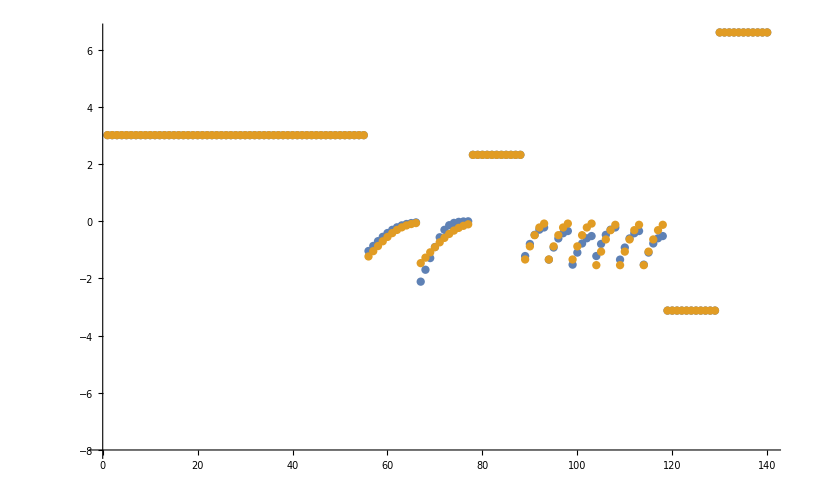

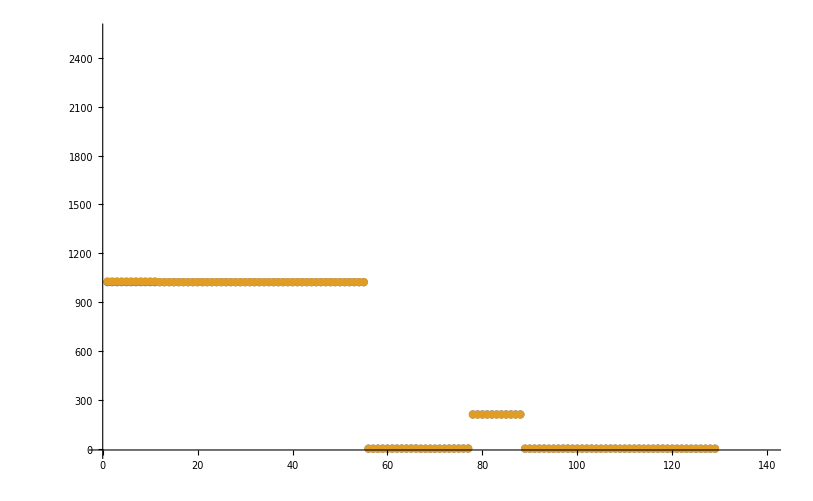

```mathematica
dataSetI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

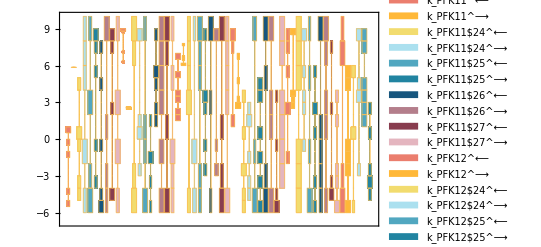

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[1;;6,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

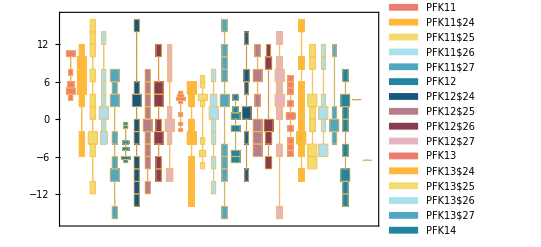

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

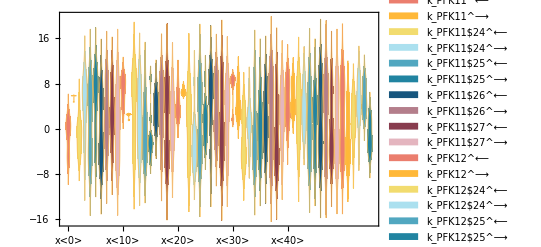

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

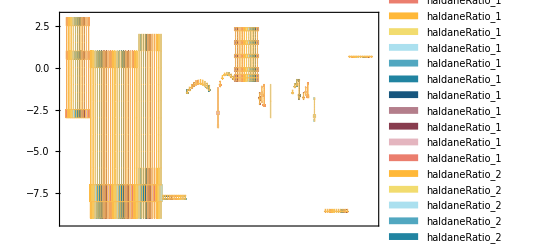

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

#### Cluster Parameters

```mathematica
(*clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Agglomerate","Linkage"->"Complete","SignificanceTest"->{"Gap","Tolerance"->0.0001}}];(**)*)
clusters=FindClusters[Log10[filteredDataList[[1;;6,2]]],Method->{"Optimize","Iterations"->2}];
medianParamCluster=Table[Median[clusters[[cluster,All,param]]],{cluster,Length[clusters]},{param,Length[clusters[[1,1]]]}](*Switch to log space and use mean?*);
clusterSqdRes=Table[(clusters[[cluster,paramSet,param]]-medianParamCluster[[cluster,param]])^2,{cluster,Length[clusters]},{paramSet,Length[clusters[[cluster]]]},{param,Length[clusters[[1,1]]]}];
clusterSSE=Table[Total[clusterSqdRes[[cluster,paramSet]]],{cluster,Length[clusterSqdRes]},{paramSet,Length[clusterSqdRes[[cluster]]]}];
bestClusterSSE=Table[SortBy[clusterSSE[[cluster]],Less],{cluster,Length[clusterSSE]}][[All,1]];
finalClusterParams={};
Table[If[clusterSSE[[cluster,paramSet]]==bestClusterSSE[[cluster]],finalClusterParams=Append[finalClusterParams,clusters[[cluster,paramSet]]]],{cluster,Length[clusterSSE]},{paramSet,Length[clusterSSE[[cluster]]]}];
```

#### Print Representative Parameter Sets for Each Cluster (Optional)

```mathematica
TableForm[finalClusterParams]
```

-1.37973 | 5.84364 | -3.5946 | -5.99984 | 3.13382 | -0.972385 | -0.374252 | 1.28276 | 8.9962 | -0.275258 | 8.99921 | 2.50734 | -2.94842 | 1.1655 | -5.23474 | -1.99025 | 5.27986 | 8.99848 | 8.08352 | -1.58515 | 2.2132 | 6.1202 | 8.99984 | -0.588219 | 5.41346 | 8.96346 | 8.99992 | 8.67113 | -5.99044 | 8.23863 | 8.99921 | 3.18931 | 0.944896 | 2.56022 | 8.54931 | 4.99545 | 5.98459 | 3.63529 | -5.68973 | 3.32948 | -1.18869 | 2.99363 | -0.373096 | 8.90056 | -1.43634 | 2.43884 | -5.98772 | -5.67567 | -4.56947 | -5.86803 | -2.30503 | 5.52468 | 5.64421 | 8.76915 | 7.24462 | 0.642565

#### Parameter Cluster Plots (Optional)

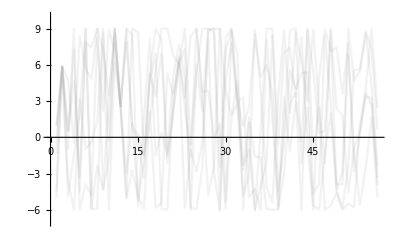

{-Graphics-}

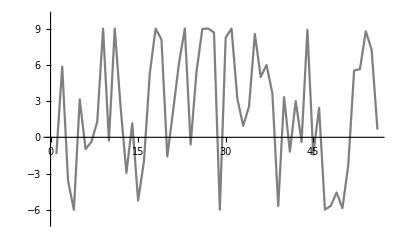

```mathematica
ListPlot[Log10[filteredDataList[[1;;6,2]]],"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]](*All parameter sets*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]]&/@clusters
(*All parameter set clusters*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[1,Gray]]&/@finalClusterParams(*Representative parameter sets*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1⟧ cannot be used as a part specification.

Keys::invrl: The argument {adp^c→1,fdp^c→1}⟦{}⟦1⟧⟧ is not a valid Association or a list of rules.

Part::pkspec1: The expression {}⟦1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

data value | predicted value | error in %
0.00009 | 0.000142232 | 58.0352
0.0042 |  |

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
210.235 | 210.25 | 0.0069566

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
1022.33 | 1022.33 | 0.000273549

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
1022.33 | 1022.33 | 0.000273549

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1⟧ cannot be used as a part specification.

Keys::invrl: The argument {adp^c→1,fdp^c→1}⟦{}⟦1⟧⟧ is not a valid Association or a list of rules.

Part::pkspec1: The expression {}⟦1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Keys::invrl: The argument {adp^c→1,fdp^c→1}⟦{}⟦1⟧⟧ is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

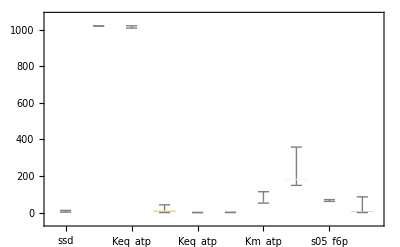

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

## Export data

```mathematica
directoryExport = "/Users/guest/Desktop/internship stuff/MASSef/examples/"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit =5;
```

/Users/guest/Desktop/internship stuff/MASSef/examples/

CreateDirectory::filex: /Users/guest/Desktop/internship stuff/MASSef/examples/pfk1 already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pfk1\rateconst_labels_pfk1.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pfk1\S_pfk1.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_PFK1[c],E_PFK1[c]@gdp,E_PFK1[c]@gdp@gdp,E_PFK1[c]@gdp@gdp@gdp,E_PFK1[c]@gdp@gdp@gdp@gdp,E_PFK1[c]&f6p,E_PFK1[c]&f6p@gdp,E_PFK1[c]&f6p@gdp@gdp,E_PFK1[c]&f6p@gdp@gdp@gdp,E_PFK1[c]&f6p@gdp@gdp@gdp@gdp,E_PFK1[c]&fdp,E_PFK1[c]&fdp@gdp,E_PFK1[c]&fdp@gdp@gdp,E_PFK1[c]&fdp@gdp@gdp@gdp,E_PFK1[c]&fdp@gdp@gdp@gdp@gdp,E_PFK1[c]&f6p&atp,E_PFK1[c]&f6p&atp@gdp,E_PFK1[c]&f6p&atp@gdp@gdp,E_PFK1[c]&f6p&atp@gdp@gdp@gdp,E_PFK1[c]&f6p&atp@gdp@gdp@gdp@gdp,E_PFK1[c]&fdp&adp,E_PFK1[c]&fdp&adp@gdp,E_PFK1[c]&fdp&adp@gdp@gdp,E_PFK1[c]&fdp&adp@gdp@gdp@gdp,E_PFK1[c]&fdp&adp@gdp@gdp@gdp@gdp,E_PFK1_T[c],E_PFK1_T[c]#pep,E_PFK1_T[c]#pep#pep,E_PFK1_T[c]#pep#pep#pep,adp[c],gdp[c],pep[c],E_PFK1_T[c]#pep#pep#pep#pep,atp[c],f6p[c],fdp[c]}

/Users/guest/Desktop/internship stuff/MASSef/examples/pfk1\species_pfk1.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{PFK11: E_PFK1[c] + f6p[c] <=> E_PFK1[c]&f6p,PFK12: E_PFK1[c]&fdp <=> E_PFK1[c] + fdp[c],PFK13: atp[c] + E_PFK1[c]&f6p <=> E_PFK1[c]&f6p&atp,PFK14: E_PFK1[c]&fdp&adp <=> adp[c] + E_PFK1[c]&fdp,PFK15: E_PFK1[c]&f6p&atp <=> E_PFK1[c]&fdp&adp,PFK11$11: E_PFK1[c]@gdp + f6p[c] <=> E_PFK1[c]&f6p@gdp,PFK12$11: E_PFK1[c]&fdp@gdp <=> E_PFK1[c]@gdp + fdp[c],PFK13$11: atp[c] + E_PFK1[c]&f6p@gdp <=> E_PFK1[c]&f6p&atp@gdp,PFK14$11: E_PFK1[c]&fdp&adp@gdp <=> adp[c] + E_PFK1[c]&fdp@gdp,PFK15$11: E_PFK1[c]&f6p&atp@gdp <=> E_PFK1[c]&fdp&adp@gdp,PFK11$12: E_PFK1[c]@gdp@gdp + f6p[c] <=> E_PFK1[c]&f6p@gdp@gdp,PFK12$12: E_PFK1[c]&fdp@gdp@gdp <=> E_PFK1[c]@gdp@gdp + fdp[c],PFK13$12: atp[c] + E_PFK1[c]&f6p@gdp@gdp <=> E_PFK1[c]&f6p&atp@gdp@gdp,PFK14$12: E_PFK1[c]&fdp&adp@gdp@gdp <=> adp[c] + E_PFK1[c]&fdp@gdp@gdp,PFK15$12: E_PFK1[c]&f6p&atp@gdp@gdp <=> E_PFK1[c]&fdp&adp@gdp@gdp,PFK11$13: E_PFK1[c]@gdp@gdp@gdp + f6p[c] <=> E_PFK1[c]&f6p@gdp@gdp@gdp,PFK12$13: E_PFK1[c]&fdp@gdp@gdp@gdp <=> E_PFK1[c]@gdp@gdp@gdp + fdp[c],PFK13$13: atp[c] + E_PFK1[c]&f6p@gdp@gdp@gdp <=> E_PFK1[c]&f6p&atp@gdp@gdp@gdp,PFK14$13: E_PFK1[c]&fdp&adp@gdp@gdp@gdp <=> adp[c] + E_PFK1[c]&fdp@gdp@gdp@gdp,PFK15$13: E_PFK1[c]&f6p&atp@gdp@gdp@gdp <=> E_PFK1[c]&fdp&adp@gdp@gdp@gdp,PFK11$14: E_PFK1[c]@gdp@gdp@gdp@gdp + f6p[c] <=> E_PFK1[c]&f6p@gdp@gdp@gdp@gdp,PFK12$14: E_PFK1[c]&fdp@gdp@gdp@gdp@gdp <=> E_PFK1[c]@gdp@gdp@gdp@gdp + fdp[c],PFK13$14: atp[c] + E_PFK1[c]&f6p@gdp@gdp@gdp@gdp <=> E_PFK1[c]&f6p&atp@gdp@gdp@gdp@gdp,PFK14$14: E_PFK1[c]&fdp&adp@gdp@gdp@gdp@gdp <=> adp[c] + E_PFK1[c]&fdp@gdp@gdp@gdp@gdp,PFK15$14: E_PFK1[c]&f6p&atp@gdp@gdp@gdp@gdp <=> E_PFK1[c]&fdp&adp@gdp@gdp@gdp@gdp,PFK1_Activation_gdp$15: E_PFK1[c] + gdp[c] <=> E_PFK1[c]@gdp,PFK1_Activation_gdp$16: E_PFK1[c]@gdp + gdp[c] <=> E_PFK1[c]@gdp@gdp,PFK1_Activation_gdp$17: E_PFK1[c]@gdp@gdp + gdp[c] <=> E_PFK1[c]@gdp@gdp@gdp,PFK1_Activation_gdp$18: E_PFK1[c]@gdp@gdp@gdp + gdp[c] <=> E_PFK1[c]@gdp@gdp@gdp@gdp,PFK1_Inhibition_pep$20: E_PFK1_T[c] + pep[c] <=> E_PFK1_T[c]#pep,PFK1_Inhibition_pep$21: E_PFK1_T[c]#pep + pep[c] <=> E_PFK1_T[c]#pep#pep,PFK1_Inhibition_pep$22: E_PFK1_T[c]#pep#pep + pep[c] <=> E_PFK1_T[c]#pep#pep#pep,PFK1_Inhibition_pep$24: E_PFK1_T[c]#pep#pep#pep + pep[c] <=> E_PFK1_T[c]#pep#pep#pep#pep,PFK1_TransitionStep: E_PFK1[c] <=> E_PFK1_T[c]}

/Users/guest/Desktop/internship stuff/MASSef/examples/pfk1\reactions_pfk1.txt

```mathematica
solEnz = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_PFK1[c],E_PFK1[c]@gdp,E_PFK1[c]@gdp@gdp,E_PFK1[c]@gdp@gdp@gdp,E_PFK1[c]@gdp@gdp@gdp@gdp,E_PFK1[c]&f6p,E_PFK1[c]&f6p@gdp,E_PFK1[c]&f6p@gdp@gdp,E_PFK1[c]&f6p@gdp@gdp@gdp,E_PFK1[c]&f6p@gdp@gdp@gdp@gdp,E_PFK1[c]&fdp,E_PFK1[c]&fdp@gdp,E_PFK1[c]&fdp@gdp@gdp,E_PFK1[c]&fdp@gdp@gdp@gdp,E_PFK1[c]&fdp@gdp@gdp@gdp@gdp,E_PFK1[c]&f6p&atp,E_PFK1[c]&f6p&atp@gdp,E_PFK1[c]&f6p&atp@gdp@gdp,E_PFK1[c]&f6p&atp@gdp@gdp@gdp,E_PFK1[c]&f6p&atp@gdp@gdp@gdp@gdp,E_PFK1[c]&fdp&adp,E_PFK1[c]&fdp&adp@gdp,E_PFK1[c]&fdp&adp@gdp@gdp,E_PFK1[c]&fdp&adp@gdp@gdp@gdp,E_PFK1[c]&fdp&adp@gdp@gdp@gdp@gdp,E_PFK1_T[c],E_PFK1_T[c]#pep,E_PFK1_T[c]#pep#pep,E_PFK1_T[c]#pep#pep#pep,E_PFK1_T[c]#pep#pep#pep#pep}

```mathematica
Sort[speciesStrings]
```

{E_PFK1[c],E_PFK1[c]&f6p,E_PFK1[c]&f6p&atp,E_PFK1[c]&f6p&atp@gdp,E_PFK1[c]&f6p&atp@gdp@gdp,E_PFK1[c]&f6p&atp@gdp@gdp@gdp,E_PFK1[c]&f6p&atp@gdp@gdp@gdp@gdp,E_PFK1[c]&f6p@gdp,E_PFK1[c]&f6p@gdp@gdp,E_PFK1[c]&f6p@gdp@gdp@gdp,E_PFK1[c]&f6p@gdp@gdp@gdp@gdp,E_PFK1[c]&fdp,E_PFK1[c]&fdp&adp,E_PFK1[c]&fdp&adp@gdp,E_PFK1[c]&fdp&adp@gdp@gdp,E_PFK1[c]&fdp&adp@gdp@gdp@gdp,E_PFK1[c]&fdp&adp@gdp@gdp@gdp@gdp,E_PFK1[c]&fdp@gdp,E_PFK1[c]&fdp@gdp@gdp,E_PFK1[c]&fdp@gdp@gdp@gdp,E_PFK1[c]&fdp@gdp@gdp@gdp@gdp,E_PFK1[c]@gdp,E_PFK1[c]@gdp@gdp,E_PFK1[c]@gdp@gdp@gdp,E_PFK1[c]@gdp@gdp@gdp@gdp,E_PFK1_T[c],E_PFK1_T[c]#pep,E_PFK1_T[c]#pep#pep,E_PFK1_T[c]#pep#pep#pep,E_PFK1_T[c]#pep#pep#pep#pep}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

(-24*k_PFK12_fwd**4*k_PFK13_rev**7*k_PFK14_fwd**5*(k_PFK12_fwd + adp(c)*k_PFK14_rev)**2*k_PFK15_rev**2*k_PFK1_Activation_gdp_rev*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_PFK1_total*param_Volume_c**21*(-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd**2*param_Volume_c**6) - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - atp(c)*k_PFK12_fwd*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*param_Volume_c**6 - adp(c)*k_PFK11_rev*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*param_Volume_c**6)**2*(-3*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*atp(c)*k_PFK12_fwd**2*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*adp(c)*k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7)*(-2*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 2*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 2*atp(c)*k_PFK12_fwd**2*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 2*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 2*adp(c)*k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7)*(4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*atp(c)*k_PFK12_fwd**2*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*adp(c)*k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7)*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**4*(-4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c)*(-24*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev**2*pep(c) - 2*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c))*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c)))) - (-(k_PFK1_TransitionStep_rev*param_Volume_c) - 4*k_PFK1_Inhibition_pep_fwd*pep(c))*(6*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c)*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))) - (-k_PFK1_Inhibition_pep_rev - 3*k_PFK1_Inhibition_pep_fwd*pep(c))*(-24*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev**2*pep(c) - 2*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c))*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c)))))))/(-(k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**3*(-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd**2*param_Volume_c**6) - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - atp(c)*k_PFK12_fwd*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*param_Volume_c**6 - adp(c)*k_PFK11_rev*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*param_Volume_c**6)*(-4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c)*(-24*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev**2*pep(c) - 2*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c))*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c)))) - (-(k_PFK1_TransitionStep_rev*param_Volume_c) - 4*k_PFK1_Inhibition_pep_fwd*pep(c))*(6*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c)*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))) - (-k_PFK1_Inhibition_pep_rev - 3*k_PFK1_Inhibition_pep_fwd*pep(c))*(-24*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev**2*pep(c) - 2*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c))*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))))))*(-((4*gdp(c)*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*k_PFK1_Activation_gdp_fwd*param_Volume_c**3*(k_PFK12_fwd*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*k_PFK15_fwd*param_Volume_c**4 - k_PFK11_rev*k_PFK13_rev*param_Volume_c**2*(adp(c)*k_PFK14_fwd*k_PFK14_rev*param_Volume_c**2 - (k_PFK12_fwd + adp(c)*k_PFK14_rev)*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**2)) - 4*gdp(c)*k_PFK13_rev*k_PFK1_Activation_gdp_fwd*param_Volume_c*(adp(c)*k_PFK14_fwd*k_PFK14_rev*param_Volume_c**2 - (k_PFK12_fwd + adp(c)*k_PFK14_rev)*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**2)*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3)))*((-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd**2*param_Volume_c**6) - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - atp(c)*k_PFK12_fwd*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*param_Volume_c**6 - adp(c)*k_PFK11_rev*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*param_Volume_c**6)*(-3*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*atp(c)*k_PFK12_fwd**2*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*adp(c)*k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7)*(4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*atp(c)*k_PFK12_fwd**2*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*adp(c)*k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7)*(2*k_PFK13_rev**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)**2*k_PFK15_rev**2*k_PFK1_Activation_gdp_rev*param_Volume_c**6*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**3*(-(k_PFK11_rev*k_PFK12_fwd**3*k_PFK13_rev**5*k_PFK14_fwd*param_Volume_c**10*(24*k_PFK14_fwd**4*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**5 + 24*k_PFK14_fwd**3*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**5)) + k_PFK12_fwd**4*k_PFK13_rev*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev**3*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**10 + 24*k_PFK13_rev**4*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**10)) + (-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK12_fwd*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**2*(-(k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-2*gdp(c)*k_PFK1_Activation_gdp_fwd - 2*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)) + k_PFK12_fwd*param_Volume_c*(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3 - fdp(c)*k_PFK12_rev*k_PFK13_rev*k_PFK15_rev*param_Volume_c**3))*(-(k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**5*k_PFK14_fwd**2*param_Volume_c**10*(24*k_PFK14_fwd**3*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4 + 24*k_PFK14_fwd**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4)) + k_PFK12_fwd**3*k_PFK13_rev**2*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev**2*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**9 + 24*k_PFK13_rev**3*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**9))) + (-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(2*gdp(c)*k_PFK12_fwd**2*k_PFK13_rev**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)**2*k_PFK15_rev**2*k_PFK1_Activation_gdp_fwd*param_Volume_c**8*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**5*k_PFK14_fwd**3*param_Volume_c**10*(24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3)) + k_PFK12_fwd**2*k_PFK13_rev**3*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8 + 24*k_PFK13_rev**2*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8)) + k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**2*(-2*k_PFK12_fwd**3*k_PFK13_rev**5*k_PFK14_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**9*(24*k_PFK14_fwd**4*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**5 + 24*k_PFK14_fwd**3*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**5) + k_PFK12_fwd*param_Volume_c*(-(k_PFK12_fwd**2*k_PFK13_rev**5*k_PFK14_fwd**2*param_Volume_c**9*(-2*gdp(c)*k_PFK1_Activation_gdp_fwd - 2*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)*(24*k_PFK14_fwd**3*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4 + 24*k_PFK14_fwd**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4)) + k_PFK12_fwd*param_Volume_c*(-2*gdp(c)*k_PFK12_fwd*k_PFK13_rev**5*k_PFK14_fwd**3*k_PFK1_Activation_gdp_fwd*param_Volume_c**9*(24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3) + k_PFK12_fwd**2*k_PFK13_rev**2*param_Volume_c**4*(-24*f6p(c)*k_PFK11_fwd*k_PFK13_rev**2*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**9 + k_PFK13_rev**3*k_PFK14_fwd**2*param_Volume_c**5*(-24*fdp(c)*k_PFK12_rev*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4 + 24*k_PFK14_fwd**3*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4)))))))) - (-((k_PFK12_fwd*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*k_PFK15_fwd*param_Volume_c**4 - k_PFK11_rev*k_PFK13_rev*param_Volume_c**2*(adp(c)*k_PFK14_fwd*k_PFK14_rev*param_Volume_c**2 - (k_PFK12_fwd + adp(c)*k_PFK14_rev)*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**2))*(-(k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-2*gdp(c)*k_PFK1_Activation_gdp_fwd - 2*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)) + k_PFK12_fwd*param_Volume_c*(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3 - fdp(c)*k_PFK12_rev*k_PFK13_rev*k_PFK15_rev*param_Volume_c**3))) + (-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK13_rev*param_Volume_c*(-2*gdp(c)*k_PFK1_Activation_gdp_fwd - 2*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)*(adp(c)*k_PFK14_fwd*k_PFK14_rev*param_Volume_c**2 - (k_PFK12_fwd + adp(c)*k_PFK14_rev)*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**2)) + k_PFK12_fwd*param_Volume_c*(-(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*k_PFK15_fwd*param_Volume_c**3) + fdp(c)*k_PFK12_rev*k_PFK13_rev*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**3)))*(-((-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd**2*param_Volume_c**6) - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - atp(c)*k_PFK12_fwd*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*param_Volume_c**6 - adp(c)*k_PFK11_rev*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*param_Volume_c**6)*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**2*(gdp(c)*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*k_PFK1_Activation_gdp_fwd*param_Volume_c**3*(k_PFK12_fwd*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*k_PFK15_fwd*param_Volume_c**4 - k_PFK11_rev*k_PFK13_rev*param_Volume_c**2*(adp(c)*k_PFK14_fwd*k_PFK14_rev*param_Volume_c**2 - (k_PFK12_fwd + adp(c)*k_PFK14_rev)*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**2)) - gdp(c)*k_PFK13_rev*k_PFK1_Activation_gdp_fwd*param_Volume_c*(adp(c)*k_PFK14_fwd*k_PFK14_rev*param_Volume_c**2 - (k_PFK12_fwd + adp(c)*k_PFK14_rev)*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**2)*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3)))*(4*k_PFK12_fwd**2*k_PFK13_rev**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)**2*k_PFK15_rev**2*k_PFK1_Activation_gdp_rev*param_Volume_c**8*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**5*k_PFK14_fwd**3*param_Volume_c**10*(24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3)) + k_PFK12_fwd**2*k_PFK13_rev**3*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8 + 24*k_PFK13_rev**2*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8)) + (-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK12_fwd**3*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**6*(-(k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-4*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)) + k_PFK12_fwd*param_Volume_c*(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3 - fdp(c)*k_PFK12_rev*k_PFK13_rev*k_PFK15_rev*param_Volume_c**3))*(-(k_PFK11_rev*k_PFK13_rev**5*k_PFK14_fwd**4*param_Volume_c**10*(24*k_PFK14_fwd*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2 + 24*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2)) + k_PFK12_fwd*k_PFK13_rev**4*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**7 + 24*k_PFK13_rev*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**7))) + k_PFK12_fwd**2*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**5*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-4*k_PFK12_fwd*k_PFK13_rev**5*k_PFK14_fwd**3*k_PFK1_Activation_gdp_rev*param_Volume_c**9*(24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3) + k_PFK12_fwd*param_Volume_c*(-(k_PFK13_rev**5*k_PFK14_fwd**4*param_Volume_c**9*(-4*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)*(24*k_PFK14_fwd*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2 + 24*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2)) + k_PFK12_fwd*k_PFK13_rev**4*param_Volume_c**5*(-24*f6p(c)*k_PFK11_fwd*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**7 + k_PFK13_rev*k_PFK14_fwd**4*param_Volume_c**5*(-24*fdp(c)*k_PFK12_rev*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2 + 24*k_PFK14_fwd*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2))))))) + (-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd**2*param_Volume_c**6) - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - atp(c)*k_PFK12_fwd*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*param_Volume_c**6 - adp(c)*k_PFK11_rev*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*param_Volume_c**6)*(4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*atp(c)*k_PFK12_fwd**2*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*adp(c)*k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7)*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(3*k_PFK12_fwd*k_PFK13_rev**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)**2*k_PFK15_rev**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**2*(-(k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**5*k_PFK14_fwd**2*param_Volume_c**10*(24*k_PFK14_fwd**3*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4 + 24*k_PFK14_fwd**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4)) + k_PFK12_fwd**3*k_PFK13_rev**2*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev**2*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**9 + 24*k_PFK13_rev**3*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**9)) + (-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK12_fwd**2*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**5*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-(gdp(c)*k_PFK1_Activation_gdp_fwd) - 3*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)) + k_PFK12_fwd*param_Volume_c*(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3 - fdp(c)*k_PFK12_rev*k_PFK13_rev*k_PFK15_rev*param_Volume_c**3))*(-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**5*k_PFK14_fwd**3*param_Volume_c**10*(24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3)) + k_PFK12_fwd**2*k_PFK13_rev**3*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8 + 24*k_PFK13_rev**2*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8))) + (-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(gdp(c)*k_PFK12_fwd**3*k_PFK13_rev**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)**2*k_PFK15_rev**2*k_PFK1_Activation_gdp_fwd*param_Volume_c**9*(-(k_PFK11_rev*k_PFK13_rev**5*k_PFK14_fwd**4*param_Volume_c**10*(24*k_PFK14_fwd*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2 + 24*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2)) + k_PFK12_fwd*k_PFK13_rev**4*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**7 + 24*k_PFK13_rev*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**7)) + k_PFK12_fwd*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-3*k_PFK12_fwd**2*k_PFK13_rev**5*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**9*(24*k_PFK14_fwd**3*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4 + 24*k_PFK14_fwd**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(-(k_PFK12_fwd*k_PFK13_rev**5*k_PFK14_fwd**3*param_Volume_c**9*(-(gdp(c)*k_PFK1_Activation_gdp_fwd) - 3*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)*(24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3)) + k_PFK12_fwd*param_Volume_c*(-(gdp(c)*k_PFK13_rev**5*k_PFK14_fwd**4*k_PFK1_Activation_gdp_fwd*param_Volume_c**9*(24*k_PFK14_fwd*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2 + 24*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2)) + k_PFK12_fwd*k_PFK13_rev**3*param_Volume_c**4*(-24*f6p(c)*k_PFK11_fwd*k_PFK13_rev*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8 + k_PFK13_rev**2*k_PFK14_fwd**3*param_Volume_c**5*(-24*fdp(c)*k_PFK12_rev*k_PFK14_fwd*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3))))))))))) + (-3*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*atp(c)*k_PFK12_fwd**2*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*adp(c)*k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7)*(-2*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 2*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 2*atp(c)*k_PFK12_fwd**2*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 2*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 2*adp(c)*k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7)*(4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*atp(c)*k_PFK12_fwd**2*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*adp(c)*k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7)*(-((-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**4*(-(k_PFK13_rev*param_Volume_c*(adp(c)*k_PFK14_fwd*k_PFK14_rev*param_Volume_c**2 - (k_PFK12_fwd + adp(c)*k_PFK14_rev)*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**2)*(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3 - fdp(c)*k_PFK12_rev*k_PFK13_rev*k_PFK15_rev*param_Volume_c**3)) + k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*k_PFK15_fwd*param_Volume_c**3) + fdp(c)*k_PFK12_rev*k_PFK13_rev*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**3))*(k_PFK12_fwd**4*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**7*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev**4*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**11 + k_PFK13_rev**5*k_PFK14_fwd**5*param_Volume_c**10*(24*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c - k_PFK11_rev*param_Volume_c*(k_PFK1_Inhibition_pep_rev*(24*k_PFK1_Inhibition_pep_rev**3 - 4*k_PFK1_Inhibition_pep_fwd*pep(c)*(12*k_PFK1_Inhibition_pep_rev**2 - 2*(-4*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c)))) - (-(k_PFK1_TransitionStep_rev*param_Volume_c) - 4*k_PFK1_Inhibition_pep_fwd*pep(c))*(2*k_PFK1_Inhibition_pep_rev*(12*k_PFK1_Inhibition_pep_rev**2 + 3*k_PFK1_Inhibition_pep_fwd*pep(c)*(-4*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))) - (-k_PFK1_Inhibition_pep_rev - 3*k_PFK1_Inhibition_pep_fwd*pep(c))*(12*k_PFK1_Inhibition_pep_rev**2 - 2*(-4*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c))))))) - k_PFK12_fwd**4*k_PFK13_rev**5*param_Volume_c**9*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3)*(24*k_PFK14_fwd**4*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**6 + k_PFK14_fwd**5*param_Volume_c**5*(24*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c - k_PFK12_fwd*param_Volume_c*(k_PFK1_Inhibition_pep_rev*(24*k_PFK1_Inhibition_pep_rev**3 - 4*k_PFK1_Inhibition_pep_fwd*pep(c)*(12*k_PFK1_Inhibition_pep_rev**2 - 2*(-4*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c)))) - (-(k_PFK1_TransitionStep_rev*param_Volume_c) - 4*k_PFK1_Inhibition_pep_fwd*pep(c))*(2*k_PFK1_Inhibition_pep_rev*(12*k_PFK1_Inhibition_pep_rev**2 + 3*k_PFK1_Inhibition_pep_fwd*pep(c)*(-4*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))) - (-k_PFK1_Inhibition_pep_rev - 3*k_PFK1_Inhibition_pep_fwd*pep(c))*(12*k_PFK1_Inhibition_pep_rev**2 - 2*(-4*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c))))))))) + (-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd**2*param_Volume_c**6) - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - atp(c)*k_PFK12_fwd*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*param_Volume_c**6 - adp(c)*k_PFK11_rev*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*param_Volume_c**6)*(4*gdp(c)*k_PFK13_rev**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)**2*k_PFK15_rev**2*k_PFK1_Activation_gdp_fwd*param_Volume_c**6*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**3*(-(k_PFK11_rev*k_PFK12_fwd**3*k_PFK13_rev**5*k_PFK14_fwd*param_Volume_c**10*(24*k_PFK14_fwd**4*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**5 + 24*k_PFK14_fwd**3*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**5)) + k_PFK12_fwd**4*k_PFK13_rev*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev**3*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**10 + 24*k_PFK13_rev**4*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**10)) + (-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**4*(-(k_PFK12_fwd**4*k_PFK13_rev**5*param_Volume_c**9*(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3 - fdp(c)*k_PFK12_rev*k_PFK13_rev*k_PFK15_rev*param_Volume_c**3)*(24*k_PFK14_fwd**4*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**6 + k_PFK14_fwd**5*param_Volume_c**5*(24*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c - k_PFK12_fwd*param_Volume_c*(k_PFK1_Inhibition_pep_rev*(24*k_PFK1_Inhibition_pep_rev**3 - 4*k_PFK1_Inhibition_pep_fwd*pep(c)*(12*k_PFK1_Inhibition_pep_rev**2 - 2*(-4*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c)))) - (-(k_PFK1_TransitionStep_rev*param_Volume_c) - 4*k_PFK1_Inhibition_pep_fwd*pep(c))*(2*k_PFK1_Inhibition_pep_rev*(12*k_PFK1_Inhibition_pep_rev**2 + 3*k_PFK1_Inhibition_pep_fwd*pep(c)*(-4*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))) - (-k_PFK1_Inhibition_pep_rev - 3*k_PFK1_Inhibition_pep_fwd*pep(c))*(12*k_PFK1_Inhibition_pep_rev**2 - 2*(-4*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c)))))))) + k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-4*gdp(c)*k_PFK12_fwd**3*k_PFK13_rev**5*k_PFK14_fwd*k_PFK1_Activation_gdp_fwd*param_Volume_c**9*(24*k_PFK14_fwd**4*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**5 + 24*k_PFK14_fwd**3*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**5) + k_PFK12_fwd**4*param_Volume_c**4*(-24*f6p(c)*k_PFK11_fwd*k_PFK13_rev**4*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**11 + k_PFK13_rev**5*param_Volume_c**5*(-24*fdp(c)*k_PFK12_rev*k_PFK14_fwd**4*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**6 + k_PFK14_fwd**5*param_Volume_c**5*(k_PFK1_TransitionStep_rev*param_Volume_c*(24*k_PFK1_Inhibition_pep_rev**4 - k_PFK1_TransitionStep_fwd*param_Volume_c*(2*k_PFK1_Inhibition_pep_rev*(12*k_PFK1_Inhibition_pep_rev**2 + 3*k_PFK1_Inhibition_pep_fwd*pep(c)*(-4*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))) - (-k_PFK1_Inhibition_pep_rev - 3*k_PFK1_Inhibition_pep_fwd*pep(c))*(12*k_PFK1_Inhibition_pep_rev**2 - 2*(-4*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c))))) - (-4*gdp(c)*k_PFK1_Activation_gdp_fwd - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c - k_PFK1_TransitionStep_fwd*param_Volume_c)*(k_PFK1_Inhibition_pep_rev*(24*k_PFK1_Inhibition_pep_rev**3 - 4*k_PFK1_Inhibition_pep_fwd*pep(c)*(12*k_PFK1_Inhibition_pep_rev**2 - 2*(-4*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c)))) - (-(k_PFK1_TransitionStep_rev*param_Volume_c) - 4*k_PFK1_Inhibition_pep_fwd*pep(c))*(2*k_PFK1_Inhibition_pep_rev*(12*k_PFK1_Inhibition_pep_rev**2 + 3*k_PFK1_Inhibition_pep_fwd*pep(c)*(-4*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))) - (-k_PFK1_Inhibition_pep_rev - 3*k_PFK1_Inhibition_pep_fwd*pep(c))*(12*k_PFK1_Inhibition_pep_rev**2 - 2*(-4*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c)))))))))))))) - (-((-(k_PFK13_rev*param_Volume_c*(adp(c)*k_PFK14_fwd*k_PFK14_rev*param_Volume_c**2 - (k_PFK12_fwd + adp(c)*k_PFK14_rev)*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**2)*(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3 - fdp(c)*k_PFK12_rev*k_PFK13_rev*k_PFK15_rev*param_Volume_c**3)) + k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*k_PFK15_fwd*param_Volume_c**3) + fdp(c)*k_PFK12_rev*k_PFK13_rev*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**3))*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4*(-4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c)*(-24*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev**2*pep(c) - 2*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c))*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c)))) - (-(k_PFK1_TransitionStep_rev*param_Volume_c) - 4*k_PFK1_Inhibition_pep_fwd*pep(c))*(6*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c)*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))) - (-k_PFK1_Inhibition_pep_rev - 3*k_PFK1_Inhibition_pep_fwd*pep(c))*(-24*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev**2*pep(c) - 2*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c))*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))))))) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3)*(-4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c)*(-24*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev**2*pep(c) - 2*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c))*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c)))) - (-(k_PFK1_TransitionStep_rev*param_Volume_c) - 4*k_PFK1_Inhibition_pep_fwd*pep(c))*(6*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c)*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))) - (-k_PFK1_Inhibition_pep_rev - 3*k_PFK1_Inhibition_pep_fwd*pep(c))*(-24*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev**2*pep(c) - 2*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c))*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c)))))))) + (-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd**2*param_Volume_c**6) - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - atp(c)*k_PFK12_fwd*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*param_Volume_c**6 - adp(c)*k_PFK11_rev*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*param_Volume_c**6)*(k_PFK12_fwd*param_Volume_c*(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3 - fdp(c)*k_PFK12_rev*k_PFK13_rev*k_PFK15_rev*param_Volume_c**3)*(-4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c)*(-24*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev**2*pep(c) - 2*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c))*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c)))) - (-(k_PFK1_TransitionStep_rev*param_Volume_c) - 4*k_PFK1_Inhibition_pep_fwd*pep(c))*(6*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c)*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))) - (-k_PFK1_Inhibition_pep_rev - 3*k_PFK1_Inhibition_pep_fwd*pep(c))*(-24*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev**2*pep(c) - 2*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c))*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c)))))) + k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-(k_PFK1_TransitionStep_fwd*k_PFK1_TransitionStep_rev*param_Volume_c**2*(6*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c)*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))) - (-k_PFK1_Inhibition_pep_rev - 3*k_PFK1_Inhibition_pep_fwd*pep(c))*(-24*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev**2*pep(c) - 2*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c))*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c)))))) - (-4*gdp(c)*k_PFK1_Activation_gdp_fwd - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c - k_PFK1_TransitionStep_fwd*param_Volume_c)*(-4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c)*(-24*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev**2*pep(c) - 2*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c))*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c)))) - (-(k_PFK1_TransitionStep_rev*param_Volume_c) - 4*k_PFK1_Inhibition_pep_fwd*pep(c))*(6*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c)*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))) - (-k_PFK1_Inhibition_pep_rev - 3*k_PFK1_Inhibition_pep_fwd*pep(c))*(-24*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev**2*pep(c) - 2*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c))*(4*k_PFK1_Inhibition_pep_fwd*k_PFK1_Inhibition_pep_rev*pep(c) + 4*k_PFK1_Inhibition_pep_rev*(-3*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c)))))))))*(-((-((k_PFK12_fwd*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*k_PFK15_fwd*param_Volume_c**4 - k_PFK11_rev*k_PFK13_rev*param_Volume_c**2*(adp(c)*k_PFK14_fwd*k_PFK14_rev*param_Volume_c**2 - (k_PFK12_fwd + adp(c)*k_PFK14_rev)*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**2))*(-(k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-3*gdp(c)*k_PFK1_Activation_gdp_fwd - k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)) + k_PFK12_fwd*param_Volume_c*(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3 - fdp(c)*k_PFK12_rev*k_PFK13_rev*k_PFK15_rev*param_Volume_c**3))) + (-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK13_rev*param_Volume_c*(-3*gdp(c)*k_PFK1_Activation_gdp_fwd - k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)*(adp(c)*k_PFK14_fwd*k_PFK14_rev*param_Volume_c**2 - (k_PFK12_fwd + adp(c)*k_PFK14_rev)*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**2)) + k_PFK12_fwd*param_Volume_c*(-(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*k_PFK15_fwd*param_Volume_c**3) + fdp(c)*k_PFK12_rev*k_PFK13_rev*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**3)))*((-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd**2*param_Volume_c**6) - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - atp(c)*k_PFK12_fwd*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*param_Volume_c**6 - adp(c)*k_PFK11_rev*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*param_Volume_c**6)*(-3*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*atp(c)*k_PFK12_fwd**2*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*adp(c)*k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7)*(4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*atp(c)*k_PFK12_fwd**2*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*adp(c)*k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7)*(2*k_PFK13_rev**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)**2*k_PFK15_rev**2*k_PFK1_Activation_gdp_rev*param_Volume_c**6*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**3*(-(k_PFK11_rev*k_PFK12_fwd**3*k_PFK13_rev**5*k_PFK14_fwd*param_Volume_c**10*(24*k_PFK14_fwd**4*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**5 + 24*k_PFK14_fwd**3*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**5)) + k_PFK12_fwd**4*k_PFK13_rev*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev**3*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**10 + 24*k_PFK13_rev**4*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**10)) + (-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK12_fwd*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**2*(-(k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-2*gdp(c)*k_PFK1_Activation_gdp_fwd - 2*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)) + k_PFK12_fwd*param_Volume_c*(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3 - fdp(c)*k_PFK12_rev*k_PFK13_rev*k_PFK15_rev*param_Volume_c**3))*(-(k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**5*k_PFK14_fwd**2*param_Volume_c**10*(24*k_PFK14_fwd**3*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4 + 24*k_PFK14_fwd**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4)) + k_PFK12_fwd**3*k_PFK13_rev**2*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev**2*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**9 + 24*k_PFK13_rev**3*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**9))) + (-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(2*gdp(c)*k_PFK12_fwd**2*k_PFK13_rev**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)**2*k_PFK15_rev**2*k_PFK1_Activation_gdp_fwd*param_Volume_c**8*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**5*k_PFK14_fwd**3*param_Volume_c**10*(24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3)) + k_PFK12_fwd**2*k_PFK13_rev**3*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8 + 24*k_PFK13_rev**2*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8)) + k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**2*(-2*k_PFK12_fwd**3*k_PFK13_rev**5*k_PFK14_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**9*(24*k_PFK14_fwd**4*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**5 + 24*k_PFK14_fwd**3*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**5) + k_PFK12_fwd*param_Volume_c*(-(k_PFK12_fwd**2*k_PFK13_rev**5*k_PFK14_fwd**2*param_Volume_c**9*(-2*gdp(c)*k_PFK1_Activation_gdp_fwd - 2*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)*(24*k_PFK14_fwd**3*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4 + 24*k_PFK14_fwd**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4)) + k_PFK12_fwd*param_Volume_c*(-2*gdp(c)*k_PFK12_fwd*k_PFK13_rev**5*k_PFK14_fwd**3*k_PFK1_Activation_gdp_fwd*param_Volume_c**9*(24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3) + k_PFK12_fwd**2*k_PFK13_rev**2*param_Volume_c**4*(-24*f6p(c)*k_PFK11_fwd*k_PFK13_rev**2*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**9 + k_PFK13_rev**3*k_PFK14_fwd**2*param_Volume_c**5*(-24*fdp(c)*k_PFK12_rev*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4 + 24*k_PFK14_fwd**3*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4)))))))) - (-((k_PFK12_fwd*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*k_PFK15_fwd*param_Volume_c**4 - k_PFK11_rev*k_PFK13_rev*param_Volume_c**2*(adp(c)*k_PFK14_fwd*k_PFK14_rev*param_Volume_c**2 - (k_PFK12_fwd + adp(c)*k_PFK14_rev)*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**2))*(-(k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-2*gdp(c)*k_PFK1_Activation_gdp_fwd - 2*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)) + k_PFK12_fwd*param_Volume_c*(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3 - fdp(c)*k_PFK12_rev*k_PFK13_rev*k_PFK15_rev*param_Volume_c**3))) + (-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK13_rev*param_Volume_c*(-2*gdp(c)*k_PFK1_Activation_gdp_fwd - 2*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)*(adp(c)*k_PFK14_fwd*k_PFK14_rev*param_Volume_c**2 - (k_PFK12_fwd + adp(c)*k_PFK14_rev)*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**2)) + k_PFK12_fwd*param_Volume_c*(-(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*k_PFK15_fwd*param_Volume_c**3) + fdp(c)*k_PFK12_rev*k_PFK13_rev*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**3)))*(-((-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd**2*param_Volume_c**6) - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - atp(c)*k_PFK12_fwd*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*param_Volume_c**6 - adp(c)*k_PFK11_rev*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*param_Volume_c**6)*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**2*(gdp(c)*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*k_PFK1_Activation_gdp_fwd*param_Volume_c**3*(k_PFK12_fwd*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*k_PFK15_fwd*param_Volume_c**4 - k_PFK11_rev*k_PFK13_rev*param_Volume_c**2*(adp(c)*k_PFK14_fwd*k_PFK14_rev*param_Volume_c**2 - (k_PFK12_fwd + adp(c)*k_PFK14_rev)*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**2)) - gdp(c)*k_PFK13_rev*k_PFK1_Activation_gdp_fwd*param_Volume_c*(adp(c)*k_PFK14_fwd*k_PFK14_rev*param_Volume_c**2 - (k_PFK12_fwd + adp(c)*k_PFK14_rev)*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**2)*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3)))*(4*k_PFK12_fwd**2*k_PFK13_rev**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)**2*k_PFK15_rev**2*k_PFK1_Activation_gdp_rev*param_Volume_c**8*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**5*k_PFK14_fwd**3*param_Volume_c**10*(24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3)) + k_PFK12_fwd**2*k_PFK13_rev**3*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8 + 24*k_PFK13_rev**2*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8)) + (-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK12_fwd**3*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**6*(-(k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-4*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)) + k_PFK12_fwd*param_Volume_c*(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3 - fdp(c)*k_PFK12_rev*k_PFK13_rev*k_PFK15_rev*param_Volume_c**3))*(-(k_PFK11_rev*k_PFK13_rev**5*k_PFK14_fwd**4*param_Volume_c**10*(24*k_PFK14_fwd*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2 + 24*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2)) + k_PFK12_fwd*k_PFK13_rev**4*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**7 + 24*k_PFK13_rev*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**7))) + k_PFK12_fwd**2*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**5*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-4*k_PFK12_fwd*k_PFK13_rev**5*k_PFK14_fwd**3*k_PFK1_Activation_gdp_rev*param_Volume_c**9*(24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3) + k_PFK12_fwd*param_Volume_c*(-(k_PFK13_rev**5*k_PFK14_fwd**4*param_Volume_c**9*(-4*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)*(24*k_PFK14_fwd*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2 + 24*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2)) + k_PFK12_fwd*k_PFK13_rev**4*param_Volume_c**5*(-24*f6p(c)*k_PFK11_fwd*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**7 + k_PFK13_rev*k_PFK14_fwd**4*param_Volume_c**5*(-24*fdp(c)*k_PFK12_rev*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2 + 24*k_PFK14_fwd*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2))))))) + (-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd**2*param_Volume_c**6) - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - atp(c)*k_PFK12_fwd*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*param_Volume_c**6 - adp(c)*k_PFK11_rev*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*param_Volume_c**6)*(4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*atp(c)*k_PFK12_fwd**2*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*adp(c)*k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7)*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(3*k_PFK12_fwd*k_PFK13_rev**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)**2*k_PFK15_rev**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**2*(-(k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**5*k_PFK14_fwd**2*param_Volume_c**10*(24*k_PFK14_fwd**3*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4 + 24*k_PFK14_fwd**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4)) + k_PFK12_fwd**3*k_PFK13_rev**2*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev**2*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**9 + 24*k_PFK13_rev**3*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**9)) + (-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK12_fwd**2*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**5*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-(gdp(c)*k_PFK1_Activation_gdp_fwd) - 3*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)) + k_PFK12_fwd*param_Volume_c*(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3 - fdp(c)*k_PFK12_rev*k_PFK13_rev*k_PFK15_rev*param_Volume_c**3))*(-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**5*k_PFK14_fwd**3*param_Volume_c**10*(24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3)) + k_PFK12_fwd**2*k_PFK13_rev**3*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8 + 24*k_PFK13_rev**2*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8))) + (-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(gdp(c)*k_PFK12_fwd**3*k_PFK13_rev**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)**2*k_PFK15_rev**2*k_PFK1_Activation_gdp_fwd*param_Volume_c**9*(-(k_PFK11_rev*k_PFK13_rev**5*k_PFK14_fwd**4*param_Volume_c**10*(24*k_PFK14_fwd*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2 + 24*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2)) + k_PFK12_fwd*k_PFK13_rev**4*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**7 + 24*k_PFK13_rev*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**7)) + k_PFK12_fwd*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-3*k_PFK12_fwd**2*k_PFK13_rev**5*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**9*(24*k_PFK14_fwd**3*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4 + 24*k_PFK14_fwd**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(-(k_PFK12_fwd*k_PFK13_rev**5*k_PFK14_fwd**3*param_Volume_c**9*(-(gdp(c)*k_PFK1_Activation_gdp_fwd) - 3*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)*(24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3)) + k_PFK12_fwd*param_Volume_c*(-(gdp(c)*k_PFK13_rev**5*k_PFK14_fwd**4*k_PFK1_Activation_gdp_fwd*param_Volume_c**9*(24*k_PFK14_fwd*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2 + 24*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2)) + k_PFK12_fwd*k_PFK13_rev**3*param_Volume_c**4*(-24*f6p(c)*k_PFK11_fwd*k_PFK13_rev*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8 + k_PFK13_rev**2*k_PFK14_fwd**3*param_Volume_c**5*(-24*fdp(c)*k_PFK12_rev*k_PFK14_fwd*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3))))))))))) + (-2*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 2*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 2*atp(c)*k_PFK12_fwd**2*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 2*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 2*adp(c)*k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7)*(-((3*gdp(c)*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*k_PFK1_Activation_gdp_fwd*param_Volume_c**3*(k_PFK12_fwd*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*k_PFK15_fwd*param_Volume_c**4 - k_PFK11_rev*k_PFK13_rev*param_Volume_c**2*(adp(c)*k_PFK14_fwd*k_PFK14_rev*param_Volume_c**2 - (k_PFK12_fwd + adp(c)*k_PFK14_rev)*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**2)) - 3*gdp(c)*k_PFK13_rev*k_PFK1_Activation_gdp_fwd*param_Volume_c*(adp(c)*k_PFK14_fwd*k_PFK14_rev*param_Volume_c**2 - (k_PFK12_fwd + adp(c)*k_PFK14_rev)*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**2)*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3)))*(-((-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd**2*param_Volume_c**6) - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - atp(c)*k_PFK12_fwd*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*param_Volume_c**6 - adp(c)*k_PFK11_rev*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*param_Volume_c**6)*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**2*(gdp(c)*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*k_PFK1_Activation_gdp_fwd*param_Volume_c**3*(k_PFK12_fwd*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*k_PFK15_fwd*param_Volume_c**4 - k_PFK11_rev*k_PFK13_rev*param_Volume_c**2*(adp(c)*k_PFK14_fwd*k_PFK14_rev*param_Volume_c**2 - (k_PFK12_fwd + adp(c)*k_PFK14_rev)*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**2)) - gdp(c)*k_PFK13_rev*k_PFK1_Activation_gdp_fwd*param_Volume_c*(adp(c)*k_PFK14_fwd*k_PFK14_rev*param_Volume_c**2 - (k_PFK12_fwd + adp(c)*k_PFK14_rev)*(k_PFK14_fwd + k_PFK15_rev)*param_Volume_c**2)*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3)))*(4*k_PFK12_fwd**2*k_PFK13_rev**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)**2*k_PFK15_rev**2*k_PFK1_Activation_gdp_rev*param_Volume_c**8*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**5*k_PFK14_fwd**3*param_Volume_c**10*(24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3)) + k_PFK12_fwd**2*k_PFK13_rev**3*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8 + 24*k_PFK13_rev**2*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8)) + (-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK12_fwd**3*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**6*(-(k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-4*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)) + k_PFK12_fwd*param_Volume_c*(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3 - fdp(c)*k_PFK12_rev*k_PFK13_rev*k_PFK15_rev*param_Volume_c**3))*(-(k_PFK11_rev*k_PFK13_rev**5*k_PFK14_fwd**4*param_Volume_c**10*(24*k_PFK14_fwd*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2 + 24*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2)) + k_PFK12_fwd*k_PFK13_rev**4*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**7 + 24*k_PFK13_rev*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**7))) + k_PFK12_fwd**2*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**5*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-4*k_PFK12_fwd*k_PFK13_rev**5*k_PFK14_fwd**3*k_PFK1_Activation_gdp_rev*param_Volume_c**9*(24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3) + k_PFK12_fwd*param_Volume_c*(-(k_PFK13_rev**5*k_PFK14_fwd**4*param_Volume_c**9*(-4*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)*(24*k_PFK14_fwd*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2 + 24*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2)) + k_PFK12_fwd*k_PFK13_rev**4*param_Volume_c**5*(-24*f6p(c)*k_PFK11_fwd*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**7 + k_PFK13_rev*k_PFK14_fwd**4*param_Volume_c**5*(-24*fdp(c)*k_PFK12_rev*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2 + 24*k_PFK14_fwd*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2))))))) + (-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd**2*param_Volume_c**6) - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - atp(c)*k_PFK12_fwd*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*param_Volume_c**6 - adp(c)*k_PFK11_rev*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*param_Volume_c**6)*(4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*atp(c)*k_PFK12_fwd**2*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*adp(c)*k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7)*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(3*k_PFK12_fwd*k_PFK13_rev**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)**2*k_PFK15_rev**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**2*(-(k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**5*k_PFK14_fwd**2*param_Volume_c**10*(24*k_PFK14_fwd**3*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4 + 24*k_PFK14_fwd**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4)) + k_PFK12_fwd**3*k_PFK13_rev**2*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev**2*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**9 + 24*k_PFK13_rev**3*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**9)) + (-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK12_fwd**2*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**5*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-(k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-(gdp(c)*k_PFK1_Activation_gdp_fwd) - 3*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)) + k_PFK12_fwd*param_Volume_c*(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3 - fdp(c)*k_PFK12_rev*k_PFK13_rev*k_PFK15_rev*param_Volume_c**3))*(-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**5*k_PFK14_fwd**3*param_Volume_c**10*(24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3)) + k_PFK12_fwd**2*k_PFK13_rev**3*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8 + 24*k_PFK13_rev**2*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8))) + (-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(gdp(c)*k_PFK12_fwd**3*k_PFK13_rev**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)**2*k_PFK15_rev**2*k_PFK1_Activation_gdp_fwd*param_Volume_c**9*(-(k_PFK11_rev*k_PFK13_rev**5*k_PFK14_fwd**4*param_Volume_c**10*(24*k_PFK14_fwd*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2 + 24*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2)) + k_PFK12_fwd*k_PFK13_rev**4*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**7 + 24*k_PFK13_rev*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**7)) + k_PFK12_fwd*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(-3*k_PFK12_fwd**2*k_PFK13_rev**5*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**9*(24*k_PFK14_fwd**3*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4 + 24*k_PFK14_fwd**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(-(k_PFK12_fwd*k_PFK13_rev**5*k_PFK14_fwd**3*param_Volume_c**9*(-(gdp(c)*k_PFK1_Activation_gdp_fwd) - 3*k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)*(24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3)) + k_PFK12_fwd*param_Volume_c*(-(gdp(c)*k_PFK13_rev**5*k_PFK14_fwd**4*k_PFK1_Activation_gdp_fwd*param_Volume_c**9*(24*k_PFK14_fwd*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2 + 24*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**2)) + k_PFK12_fwd*k_PFK13_rev**3*param_Volume_c**4*(-24*f6p(c)*k_PFK11_fwd*k_PFK13_rev*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**8 + k_PFK13_rev**2*k_PFK14_fwd**3*param_Volume_c**5*(-24*fdp(c)*k_PFK12_rev*k_PFK14_fwd*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3 + 24*k_PFK14_fwd**2*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**3)))))))))) + (-(k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd**2*param_Volume_c**6) - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - atp(c)*k_PFK12_fwd*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*param_Volume_c**6 - k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*param_Volume_c**6 - adp(c)*k_PFK11_rev*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*param_Volume_c**6)*(-3*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*atp(c)*k_PFK12_fwd**2*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7 - 3*adp(c)*k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7)*(4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd**2*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*atp(c)*k_PFK12_fwd**2*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd**2*k_PFK15_fwd*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**2*k_PFK14_fwd*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7 + 4*adp(c)*k_PFK11_rev*k_PFK12_fwd*k_PFK13_rev**2*k_PFK14_fwd*k_PFK14_rev*k_PFK15_rev*k_PFK1_Activation_gdp_rev*param_Volume_c**7)*(-(k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**3*(-(k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-3*gdp(c)*k_PFK1_Activation_gdp_fwd - k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)) + k_PFK12_fwd*param_Volume_c*(f6p(c)*k_PFK11_fwd*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3 - fdp(c)*k_PFK12_rev*k_PFK13_rev*k_PFK15_rev*param_Volume_c**3))*(-(k_PFK11_rev*k_PFK12_fwd**3*k_PFK13_rev**5*k_PFK14_fwd*param_Volume_c**10*(24*k_PFK14_fwd**4*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**5 + 24*k_PFK14_fwd**3*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**5)) + k_PFK12_fwd**4*k_PFK13_rev*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev**3*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**10 + 24*k_PFK13_rev**4*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**10))) + (-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))*(3*gdp(c)*k_PFK12_fwd*k_PFK13_rev**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)**2*k_PFK15_rev**2*k_PFK1_Activation_gdp_fwd*param_Volume_c**7*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**2*(-(k_PFK11_rev*k_PFK12_fwd**2*k_PFK13_rev**5*k_PFK14_fwd**2*param_Volume_c**10*(24*k_PFK14_fwd**3*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4 + 24*k_PFK14_fwd**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4)) + k_PFK12_fwd**3*k_PFK13_rev**2*param_Volume_c**5*(24*(k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK13_rev**2*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**9 + 24*k_PFK13_rev**3*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**9)) + k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**3*(-(k_PFK11_rev*k_PFK13_rev*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK15_rev*param_Volume_c**4) + k_PFK12_fwd*param_Volume_c*(atp(c)*k_PFK13_fwd*k_PFK13_rev*k_PFK14_fwd*param_Volume_c**3 - (k_PFK11_rev + atp(c)*k_PFK13_fwd)*k_PFK14_fwd*(k_PFK13_rev + k_PFK15_fwd)*param_Volume_c**3))**3*(-(k_PFK12_fwd**3*k_PFK13_rev**5*k_PFK14_fwd*param_Volume_c**9*(-3*gdp(c)*k_PFK1_Activation_gdp_fwd - k_PFK1_Activation_gdp_rev - f6p(c)*k_PFK11_fwd*param_Volume_c - fdp(c)*k_PFK12_rev*param_Volume_c)*(24*k_PFK14_fwd**4*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**5 + 24*k_PFK14_fwd**3*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**5)) + k_PFK12_fwd*param_Volume_c*(-3*gdp(c)*k_PFK12_fwd**2*k_PFK13_rev**5*k_PFK14_fwd**2*k_PFK1_Activation_gdp_fwd*param_Volume_c**9*(24*k_PFK14_fwd**3*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4 + 24*k_PFK14_fwd**2*(k_PFK12_fwd + adp(c)*k_PFK14_rev)*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**4) + k_PFK12_fwd**3*k_PFK13_rev*param_Volume_c**4*(-24*f6p(c)*k_PFK11_fwd*k_PFK13_rev**3*k_PFK14_fwd**5*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**10 + k_PFK13_rev**4*k_PFK14_fwd*param_Volume_c**5*(-24*fdp(c)*k_PFK12_rev*k_PFK14_fwd**3*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c**5 + k_PFK14_fwd**4*param_Volume_c**4*(24*k_PFK1_Inhibition_pep_rev**4*k_PFK1_TransitionStep_rev*param_Volume_c - k_PFK1_Activation_gdp_rev*(k_PFK1_Inhibition_pep_rev*(24*k_PFK1_Inhibition_pep_rev**3 - 4*k_PFK1_Inhibition_pep_fwd*pep(c)*(12*k_PFK1_Inhibition_pep_rev**2 - 2*(-4*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c)))) - (-(k_PFK1_TransitionStep_rev*param_Volume_c) - 4*k_PFK1_Inhibition_pep_fwd*pep(c))*(2*k_PFK1_Inhibition_pep_rev*(12*k_PFK1_Inhibition_pep_rev**2 + 3*k_PFK1_Inhibition_pep_fwd*pep(c)*(-4*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))) - (-k_PFK1_Inhibition_pep_rev - 3*k_PFK1_Inhibition_pep_fwd*pep(c))*(12*k_PFK1_Inhibition_pep_rev**2 - 2*(-4*k_PFK1_Inhibition_pep_rev - k_PFK1_Inhibition_pep_fwd*pep(c))*(k_PFK1_Inhibition_pep_rev + k_PFK1_Inhibition_pep_fwd*pep(c)))))))))))))))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pfk1\rateconst_clusters_pfk1.txt

```mathematica
solRateEq = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
```

```mathematica
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pfk1\rateLaw_pfk1.txt